```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp3/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{4915.,5054.,4961.,5359.,5172.,5007.,4824.,4687.,4830.,5051.,5001.,4844.,4682.,4630.,4782.,4935.,5344.,5967.,5159.,5354.,4322.,4882.,5001.,4999.,5469.,5092.,5209.,5082.,5455.,5506.,5259.,4846.,4889.,5162.,5154.,4726.,5395.,5419.,5338.,4410.,4477.,4826.,4869.,5195.,4710.,5543.,4619.,5030.,4931.,5552.,4971.,4769.,4886.,5504.,4679.,5098.,5451.,4536.,5868.,4784.,4942.,5594.,5203.,4793.,4550.,4888.,4726.,6075.,4973.,4924.,4902.,4745.,5214.,5572.,5051.,4522.,5072.,5028.,5765.,5031.,5507.,5636.,5158.,5173.,5186.,4412.,5727.,5862.,5479.,4717.,5154.,4849.,4854.,4914.,5320.,4793.,5559.,4561.,5103.,4758.}

{3126.,3706.,3273.,4022.,3486.,3932.,3751.,3309.,3600.,3284.,3808.,3380.,3116.,3213.,3316.,3521.,3688.,3593.,3532.,3846.,2994.,4056.,3630.,3563.,3257.,3470.,3451.,3469.,3889.,3776.,3358.,3392.,3494.,4262.,3292.,3246.,3565.,3240.,3720.,3624.,3201.,3583.,3457.,3455.,3907.,3456.,3189.,4611.,3046.,3373.,3492.,3396.,3389.,3300.,3340.,3771.,3632.,4114.,3269.,3429.,3365.,3539.,3504.,3552.,3351.,4029.,3091.,3172.,3800.,3217.,3277.,3870.,3568.,3749.,3545.,3369.,4035.,4423.,3221.,3829.,3939.,3229.,4147.,3728.,3047.,3122.,3820.,4268.,3436.,4025.,3009.,4032.,3902.,3537.,3662.,3325.,2924.,4218.,3648.,3164.}

{3529.,3827.,3640.,3127.,3451.,3437.,3240.,3337.,3509.,3787.,3711.,3236.,3665.,3472.,3290.,3326.,3593.,3132.,3323.,3773.,3581.,3476.,3833.,3607.,3443.,3571.,3639.,3577.,3535.,3434.,3446.,3229.,3340.,3411.,3283.,3367.,3290.,3886.,3664.,3439.,3431.,3190.,3275.,4198.,3511.,3977.,3192.,3560.,3927.,3764.,3417.,3729.,3397.,4057.,3180.,3524.,3786.,3519.,3554.,3681.,3530.,3423.,3476.,3303.,3084.,3122.,3522.,3375.,3678.,3706.,3531.,3459.,4055.,3520.,3147.,3406.,3223.,3906.,3284.,3382.,3512.,3375.,3494.,3413.,3303.,3515.,3279.,3566.,3266.,3729.,3256.,3623.,3410.,3837.,3599.,3742.,3671.,3244.,3657.,3390.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{4428.,5071.,4236.,3686.,4075.,4009.,3891.,4080.,4243.,4323.,3474.,4384.,4225.,4161.,4245.,4258.,4361.,4073.,4394.,4190.,4272.,4437.,3442.,4020.,3894.,4180.,4184.,4177.,4322.,4211.,3934.,4169.,3912.,4195.,4781.,4254.,4191.,3935.,4127.,4798.,4784.,4323.,4103.,4450.,4630.,4716.,4339.,4800.,4207.,4214.,4128.,4006.,3992.,3516.,4421.,3923.,4406.,3726.,4628.,4465.,3753.,3683.,4236.,4351.,4441.,4378.,4564.,4035.,4159.,3601.,4728.,3774.,4875.,4410.,4171.,3784.,4137.,3877.,4748.,3751.,4245.,4339.,3903.,4103.,3990.,4064.,4038.,3981.,4604.,4695.,4221.,3868.,4005.,4415.,4222.,3934.,4257.,3938.,5166.,4068.}

Part::partd: Part specification lrandommm ⟦ 2000 ⟧ is longer than depth of object.

lrandommm⟦2000⟧

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3576.,3476.,3863.,3690.,3511.,3492.,3518.,3350.,3453.,3382.,3702.,3212.,3846.,3451.,3938.,3731.,3812.,3416.,3173.,3806.,3932.,3613.,3344.,3323.,3936.,3492.,3726.,3346.,3448.,3788.,3829.,3612.,3545.,3541.,3675.,3621.,3270.,3837.,3524.,3469.,3682.,3543.,3596.,3219.,3588.,3375.,3961.,3559.,3413.,3478.,3855.,3365.,3729.,3613.,3121.,3316.,3379.,3802.,3506.,3817.,3324.,3219.,3800.,3302.,3337.,3746.,3511.,3600.,3697.,3415.,3588.,3615.,3401.,3639.,3406.,3541.,3336.,3693.,3734.,3603.,3568.,3402.,3703.,4065.,3545.,3318.,3756.,3417.,3845.,3423.,3335.,3985.,4008.,3887.,3658.,3478.,3346.,3654.,3537.,3471.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,4915.},{1,5054.},{1,4961.},{1,5359.},{1,5172.},{1,5007.},{1,4824.},{1,4687.},{1,4830.},{1,5051.},{1,5001.},{1,4844.},{1,4682.},{1,4630.},{1,4782.},{1,4935.},{1,5344.},{1,5967.},{1,5159.},{1,5354.},{1,4322.},{1,4882.},{1,5001.},{1,4999.},{1,5469.},{1,5092.},{1,5209.},{1,5082.},{1,5455.},{1,5506.},{1,5259.},{1,4846.},{1,4889.},{1,5162.},{1,5154.},{1,4726.},{1,5395.},{1,5419.},{1,5338.},{1,4410.},{1,4477.},{1,4826.},{1,4869.},{1,5195.},{1,4710.},{1,5543.},{1,4619.},{1,5030.},{1,4931.},{1,5552.},{1,4971.},{1,4769.},{1,4886.},{1,5504.},{1,4679.},{1,5098.},{1,5451.},{1,4536.},{1,5868.},{1,4784.},{1,4942.},{1,5594.},{1,5203.},{1,4793.},{1,4550.},{1,4888.},{1,4726.},{1,6075.},{1,4973.},{1,4924.},{1,4902.},{1,4745.},{1,5214.},{1,5572.},{1,5051.},{1,4522.},{1,5072.},{1,5028.},{1,5765.},{1,5031.},{1,5507.},{1,5636.},{1,5158.},{1,5173.},{1,5186.},{1,4412.},{1,5727.},{1,5862.},{1,5479.},{1,4717.},{1,5154.},{1,4849.},{1,4854.},{1,4914.},{1,5320.},{1,4793.},{1,5559.},{1,4561.},{1,5103.},{1,4758.}}

{{2,3126.},{2,3706.},{2,3273.},{2,4022.},{2,3486.},{2,3932.},{2,3751.},{2,3309.},{2,3600.},{2,3284.},{2,3808.},{2,3380.},{2,3116.},{2,3213.},{2,3316.},{2,3521.},{2,3688.},{2,3593.},{2,3532.},{2,3846.},{2,2994.},{2,4056.},{2,3630.},{2,3563.},{2,3257.},{2,3470.},{2,3451.},{2,3469.},{2,3889.},{2,3776.},{2,3358.},{2,3392.},{2,3494.},{2,4262.},{2,3292.},{2,3246.},{2,3565.},{2,3240.},{2,3720.},{2,3624.},{2,3201.},{2,3583.},{2,3457.},{2,3455.},{2,3907.},{2,3456.},{2,3189.},{2,4611.},{2,3046.},{2,3373.},{2,3492.},{2,3396.},{2,3389.},{2,3300.},{2,3340.},{2,3771.},{2,3632.},{2,4114.},{2,3269.},{2,3429.},{2,3365.},{2,3539.},{2,3504.},{2,3552.},{2,3351.},{2,4029.},{2,3091.},{2,3172.},{2,3800.},{2,3217.},{2,3277.},{2,3870.},{2,3568.},{2,3749.},{2,3545.},{2,3369.},{2,4035.},{2,4423.},{2,3221.},{2,3829.},{2,3939.},{2,3229.},{2,4147.},{2,3728.},{2,3047.},{2,3122.},{2,3820.},{2,4268.},{2,3436.},{2,4025.},{2,3009.},{2,4032.},{2,3902.},{2,3537.},{2,3662.},{2,3325.},{2,2924.},{2,4218.},{2,3648.},{2,3164.}}

{{3,3529.},{3,3827.},{3,3640.},{3,3127.},{3,3451.},{3,3437.},{3,3240.},{3,3337.},{3,3509.},{3,3787.},{3,3711.},{3,3236.},{3,3665.},{3,3472.},{3,3290.},{3,3326.},{3,3593.},{3,3132.},{3,3323.},{3,3773.},{3,3581.},{3,3476.},{3,3833.},{3,3607.},{3,3443.},{3,3571.},{3,3639.},{3,3577.},{3,3535.},{3,3434.},{3,3446.},{3,3229.},{3,3340.},{3,3411.},{3,3283.},{3,3367.},{3,3290.},{3,3886.},{3,3664.},{3,3439.},{3,3431.},{3,3190.},{3,3275.},{3,4198.},{3,3511.},{3,3977.},{3,3192.},{3,3560.},{3,3927.},{3,3764.},{3,3417.},{3,3729.},{3,3397.},{3,4057.},{3,3180.},{3,3524.},{3,3786.},{3,3519.},{3,3554.},{3,3681.},{3,3530.},{3,3423.},{3,3476.},{3,3303.},{3,3084.},{3,3122.},{3,3522.},{3,3375.},{3,3678.},{3,3706.},{3,3531.},{3,3459.},{3,4055.},{3,3520.},{3,3147.},{3,3406.},{3,3223.},{3,3906.},{3,3284.},{3,3382.},{3,3512.},{3,3375.},{3,3494.},{3,3413.},{3,3303.},{3,3515.},{3,3279.},{3,3566.},{3,3266.},{3,3729.},{3,3256.},{3,3623.},{3,3410.},{3,3837.},{3,3599.},{3,3742.},{3,3671.},{3,3244.},{3,3657.},{3,3390.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,4428.},{7,5071.},{7,4236.},{7,3686.},{7,4075.},{7,4009.},{7,3891.},{7,4080.},{7,4243.},{7,4323.},{7,3474.},{7,4384.},{7,4225.},{7,4161.},{7,4245.},{7,4258.},{7,4361.},{7,4073.},{7,4394.},{7,4190.},{7,4272.},{7,4437.},{7,3442.},{7,4020.},{7,3894.},{7,4180.},{7,4184.},{7,4177.},{7,4322.},{7,4211.},{7,3934.},{7,4169.},{7,3912.},{7,4195.},{7,4781.},{7,4254.},{7,4191.},{7,3935.},{7,4127.},{7,4798.},{7,4784.},{7,4323.},{7,4103.},{7,4450.},{7,4630.},{7,4716.},{7,4339.},{7,4800.},{7,4207.},{7,4214.},{7,4128.},{7,4006.},{7,3992.},{7,3516.},{7,4421.},{7,3923.},{7,4406.},{7,3726.},{7,4628.},{7,4465.},{7,3753.},{7,3683.},{7,4236.},{7,4351.},{7,4441.},{7,4378.},{7,4564.},{7,4035.},{7,4159.},{7,3601.},{7,4728.},{7,3774.},{7,4875.},{7,4410.},{7,4171.},{7,3784.},{7,4137.},{7,3877.},{7,4748.},{7,3751.},{7,4245.},{7,4339.},{7,3903.},{7,4103.},{7,3990.},{7,4064.},{7,4038.},{7,3981.},{7,4604.},{7,4695.},{7,4221.},{7,3868.},{7,4005.},{7,4415.},{7,4222.},{7,3934.},{7,4257.},{7,3938.},{7,5166.},{7,4068.}}

Part::partw: Part {8, 2000} of {8, lrandommm} does not exist.

{8,lrandommm}⟦{8,2000}⟧

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3576.},{10,3476.},{10,3863.},{10,3690.},{10,3511.},{10,3492.},{10,3518.},{10,3350.},{10,3453.},{10,3382.},{10,3702.},{10,3212.},{10,3846.},{10,3451.},{10,3938.},{10,3731.},{10,3812.},{10,3416.},{10,3173.},{10,3806.},{10,3932.},{10,3613.},{10,3344.},{10,3323.},{10,3936.},{10,3492.},{10,3726.},{10,3346.},{10,3448.},{10,3788.},{10,3829.},{10,3612.},{10,3545.},{10,3541.},{10,3675.},{10,3621.},{10,3270.},{10,3837.},{10,3524.},{10,3469.},{10,3682.},{10,3543.},{10,3596.},{10,3219.},{10,3588.},{10,3375.},{10,3961.},{10,3559.},{10,3413.},{10,3478.},{10,3855.},{10,3365.},{10,3729.},{10,3613.},{10,3121.},{10,3316.},{10,3379.},{10,3802.},{10,3506.},{10,3817.},{10,3324.},{10,3219.},{10,3800.},{10,3302.},{10,3337.},{10,3746.},{10,3511.},{10,3600.},{10,3697.},{10,3415.},{10,3588.},{10,3615.},{10,3401.},{10,3639.},{10,3406.},{10,3541.},{10,3336.},{10,3693.},{10,3734.},{10,3603.},{10,3568.},{10,3402.},{10,3703.},{10,4065.},{10,3545.},{10,3318.},{10,3756.},{10,3417.},{10,3845.},{10,3423.},{10,3335.},{10,3985.},{10,4008.},{10,3887.},{10,3658.},{10,3478.},{10,3346.},{10,3654.},{10,3537.},{10,3471.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 1.81012×10^8 | 4.5253×10^7 | 499.443 | 3.43137×10^-172
Error | 495 | 4.48504×10^7 | 90606.9 |  | 
Total | 499 | 2.25862×10^8 |  |  | ,CellMeans→All | 3980.15
Model[1] | 5067.63
Model[2] | 3553.48
Model[3] | 3503.38
Model[7] | 4205.31
Model[10] | 3570.94,PostTests→{Model→Tukey | {{1,2},{1,3},{1,7},{2,7},{3,7},{1,10},{7,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[randommm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[randommm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[randommm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

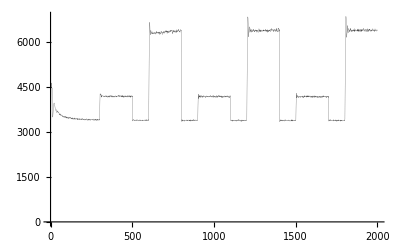

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.,3828.05,5271.01,6273.03,6941.86,7148.49,7238.74,7073.9,6974.66,6933.9,6825.52,6753.35,6561.42,6223.33,5873.9,5591.42,5146.65,4859.93,4604.46,4414.93,4397.98,4394.77,4388.68,4323.82,4396.01,4351.74,4378.88,4313.39,4332.6,4365.95,4399.96,4428.77,4435.93,4491.27,4483.51,4523.79,4450.85,4465.16,4429.15,4448.39,4455.89,4365.54,4300.41,4324.84,4345.42,4313.26,4242.05,4225.14,4191.51,4133.46,4163.39,4113.49,4087.64,4010.59,4030.37,3967.61,3897.7,3921.18,3877.77,3859.14,3838.07,3855.22,3853.2,3778.38,3781.57,3765.23,3773.3,3746.63,3761.47,3747.87,3719.97,3661.79,3657.22,3657.82,3643.95,3659.53,3625.73,3654.37,3663.52,3646.47,3599.35,3575.1,3602.38,3642.14,3623.98,3578.48,3578.57,3586.48,3590.75,3574.6,3577.91,3570.87,3559.74,3541.65,3583.08,3560.43,3565.34,3603.29,3589.,3557.4,3530.42,3517.08,3562.09,3530.59,3547.4,3547.44,3529.97,3505.57,3513.33,3521.07,3551.12,3483.91,3535.24,3532.73,3544.82,3527.69,3529.81,3512.9,3502.06,3527.08,3497.77,3507.76,3525.17,3506.73,3520.5,3538.5,3512.17,3502.34,3538.4,3527.01,3495.77,3538.83,3509.67,3521.57,3483.52,3484.47,3487.98,3491.69,3475.88,3506.83,3472.42,3478.7,3519.65,3494.42,3489.6,3512.23,3491.81,3472.64,3492.62,3502.83,3493.84,3474.42,3473.73,3454.24,3497.49,3489.65,3491.34,3498.47,3461.25,3473.07,3496.85,3473.28,3482.03,3473.12,3482.2,3498.82,3462.62,3485.68,3481.08,3494.08,3503.26,3449.61,3519.02,3490.69,3480.47,3491.07,3483.52,3467.19,3478.85,3499.88,3477.23,3459.27,3489.42,3487.75,3502.9,3501.58,3467.49,3496.66,3469.89,3443.59,3484.66,3482.57,3446.99,3458.44,3462.42,3464.87,3465.44,3491.58,3469.,3466.41,3487.48,3429.17,3485.39,3471.93,3509.1,3451.75,3470.34,3507.86,3486.56,3466.86,3440.58,3473.22,3465.35,3464.81,3483.7,3478.11,3433.69,3469.8,3493.53,3421.96,3482.86,3494.87,3488.91,3452.37,3460.09,3467.21,3479.6,3466.79,3469.02,3463.17,3459.33,3458.14,3476.34,3489.98,3481.63,3448.57,3491.57,3497.81,3486.74,3479.9,3465.59,3456.06,3472.32,3495.32,3476.34,3460.44,3460.57,3463.7,3478.65,3458.71,3463.03,4303.54,4720.81,4807.61,4734.98,4639.84,4580.64,4581.73,4535.72,4487.94,4444.88,4424.54,4385.35,4302.08,4286.41,4286.12,4221.91,4192.82,4173.82,4110.95,4067.29,4075.18,4071.8,4044.59,4041.85,4006.68,3950.37,3952.11,3937.96,3920.35,3888.55,3893.07,3886.48,3902.34,3872.5,3847.48,3878.76,3888.49,3888.77,3822.66,3859.77,3845.75,3800.29,3799.25,3794.75,3762.57,3832.16,3811.74,3766.61,3727.47,3774.58,3758.56,3725.65,3752.45,3714.82,3706.62,3746.18,3765.28,3733.09,3711.08,3710.21,3691.1,3696.75,3717.4,3699.53,3692.46,3685.5,3703.37,3728.41,3702.77,3698.55,3698.02,3708.49,3701.24,3672.74,3688.52,3690.06,3681.29,3652.29,3694.58,3673.8,3686.18,3675.29,3677.41,3655.27,3639.43,3705.95,3708.93,3695.86,3674.77,3668.05,3662.26,3639.73,3691.99,3687.79,3633.98,3666.1,3647.19,3661.25,3669.62,3667.97,3677.63,3666.72,3664.76,3648.08,3677.7,3640.43,3645.6,3611.14,3679.81,3642.35,3655.26,3679.92,3686.57,3635.81,3612.4,3663.08,3657.84,3648.62,3663.01,3632.63,3635.26,3665.86,3643.15,3628.88,3663.06,3647.81,3644.35,3653.91,3600.91,3611.66,3647.82,3624.22,3630.94,3648.65,3630.35,3649.31,3652.18,3638.56,3644.98,3639.08,3649.72,3599.24,3645.13,3627.99,3599.73,3622.07,3607.5,3659.91,3651.34,3600.83,3662.38,3641.33,3619.23,3601.64,3642.55,3611.16,3627.44,3606.68,3620.16,3625.03,3635.5,3620.96,3651.17,3632.41,3634.7,3615.13,3636.75,3609.94,3607.52,3592.54,3613.42,3579.85,3604.21,3625.72,3606.23,3609.53,3607.45,3601.4,3590.55,3636.03,3628.86,3634.01,3619.86,3615.74,3640.19,3606.94,3613.,3602.38,3614.28,3621.96,3651.68,3617.42,3603.77,3593.99,3616.85,3622.63,3633.23,3601.19,3597.62,3605.75,3601.94,3619.98,3674.55,3641.19,3634.55,3606.8,3601.4,3614.94,3614.8,3634.95,3605.62,3588.08,3621.84,3618.41,3631.02,3623.83,3606.43,3629.11,3651.33,3620.73,3624.5,3616.76,3614.78,3601.3,3580.32,3594.21,3597.09,3626.64,3585.95,3651.34,3616.75,3607.59,3623.81,3593.46,3568.04,3597.,3575.65,3606.71,3574.61,3605.03,3625.04,3603.05,3597.9,3623.98,3620.52,3591.65,3608.87,3640.35,3601.65,3610.67,4588.62,5498.41,5969.69,5994.7,5745.66,5603.48,5568.35,5486.91,5417.62,5369.57,5247.22,5197.6,5051.71,5009.65,4953.46,4868.03,4812.74,4822.38,4739.02,4644.69,4596.56,4573.18,4573.19,4547.46,4486.04,4445.62,4395.9,4413.86,4328.61,4319.82,4325.78,4329.13,4265.71,4252.29,4257.37,4283.41,4273.39,4214.78,4220.47,4238.67,4202.52,4189.78,4163.94,4166.31,4189.78,4169.1,4088.95,4073.13,4082.17,4076.75,4102.64,4076.9,4041.07,4037.18,4041.9,4084.42,4008.45,3998.6,4003.22,4025.04,4000.74,4025.51,3977.69,3961.87,4004.1,3983.61,3958.24,3951.48,3996.91,3993.94,3970.91,3997.24,3977.49,3970.19,3937.93,3945.46,3938.53,3957.97,3922.56,3919.76,3891.,3942.69,3928.36,3963.91,3908.2,3870.61,3852.05,3875.49,3892.77,3856.3,3885.5,3841.,3874.94,3857.1,3858.29,3863.17,3859.02,3860.17,3858.03,3913.6,3869.97,3844.72,3854.5,3862.46,3852.18,3855.79,3875.03,3846.12,3840.46,3875.25,3837.84,3830.7,3844.32,3832.97,3829.03,3865.44,3867.44,3829.87,3778.85,3811.04,3824.71,3840.6,3848.75,3841.98,3818.71,3795.88,3834.74,3803.85,3773.33,3830.2,3862.52,3843.99,3770.55,3825.39,3789.05,3827.48,3795.05,3803.32,3828.85,3825.29,3825.5,3807.56,3809.03,3791.84,3814.58,3796.74,3793.86,3793.1,3780.03,3765.43,3792.95,3775.29,3773.5,3791.99,3780.69,3806.86,3768.73,3824.41,3802.21,3804.32,3812.77,3816.11,3818.24,3781.95,3801.14,3798.24,3800.58,3811.06,3779.76,3811.66,3798.8,3779.55,3799.05,3798.31,3787.59,3830.79,3771.28,3738.06,3783.22,3776.91,3782.71,3781.31,3772.79,3781.51,3777.56,3792.55,3778.74,3736.51,3789.95,3792.37,3778.06,3730.26,3747.18,3781.2,3746.89,3792.35,3756.98,3748.17,3774.41,3765.33,3774.18,3743.91,3778.79,3756.05,3761.04,3783.45,3775.27,3767.3,3792.92,3778.77,3752.03,3756.15,3750.37,3767.17,3798.98,3742.99,3751.87,3808.97,3764.28,3714.42,3751.19,3779.85,3761.81,3752.82,3740.67,3755.06,3782.37,3766.63,3778.48,3761.78,3750.37,3753.42,3759.03,3760.68,3784.77,3782.83,3780.84,3780.59,3789.96,3781.27,3722.51,3714.06,3750.93,3724.77,3724.75,3782.74,3727.59,3734.69,3738.05,3755.5,4685.21,5604.27,5919.68,5972.14,5708.15,5544.06,5408.93,5492.8,5506.96,5306.85,5263.47,5230.54,5163.01,5073.77,4988.82,4887.43,4825.39,4759.33,4755.81,4708.52,4675.9,4607.99,4584.59,4578.82,4540.85,4458.2,4452.36,4475.08,4424.93,4402.94,4302.55,4376.79,4365.75,4286.54,4297.02,4306.06,4304.01,4276.96,4226.9,4200.49,4254.54,4213.94,4190.26,4216.99,4211.5,4172.55,4207.13,4171.21,4175.44,4199.01,4157.67,4136.7,4124.94,4099.62,4141.44,4118.18,4116.95,4140.55,4087.44,4091.85,4056.31,4083.85,4109.38,4088.41,4071.58,4108.4,4059.04,4067.51,4032.16,4027.83,4026.13,4075.1,4058.6,4014.03,4011.89,3993.91,4031.72,3994.55,4015.18,4037.97,4010.82,3996.73,3976.1,3980.16,4005.69,3999.24,4006.27,3986.37,4002.12,3984.22,3993.21,3991.4,4017.97,3983.97,3997.27,3943.56,3935.73,3957.3,3954.43,3951.42,3964.88,3970.36,3984.2,3960.37,3978.38,3941.43,3945.49,3984.49,3955.98,3967.09,3947.14,3954.93,3980.2,3948.28,3914.02,3960.07,3933.96,3908.51,3964.26,3963.72,3952.08,3935.83,3961.47,3941.56,3946.71,3952.02,3950.25,3949.47,3938.54,3945.3,3922.16,3912.84,3961.12,3930.39,3973.26,3975.18,3926.07,3904.97,3916.58,3950.8,3933.55,3938.44,3898.73,3853.02,3907.24,3921.75,3903.72,3854.24,3898.29,3901.78,3880.55,3927.45,3909.25,3895.66,3929.15,3875.5,3888.6,3893.48,3927.34,3897.28,3869.04,3905.35,3903.85,3893.09,3880.94,3895.96,3934.45,3911.77,3921.2,3912.26,3933.03,3887.32,3901.17,3891.58,3885.35,3898.6,3881.52,3881.71,3855.5,3866.59,3894.81,3851.12,3856.37,3883.34,3887.07,3884.27,3895.76,3823.11,3875.84,3861.59,3867.42,3883.36,3859.3,3862.49,3914.84,3879.14,3877.71,3846.25,3853.43,3864.14,3859.78,3867.88,3875.98,3871.38,3899.73,3896.15,3843.64,3848.12,3855.58,3900.29,3850.41,3835.04,3879.29,3840.21,3854.94,3880.3,3897.81,3870.24,3881.18,3849.95,3852.46,3875.52,3865.97,3918.22,3882.46,3888.14,3867.18,3860.75,3863.42,3874.09,3905.59,3885.78,3853.29,3803.38,3836.71,3881.66,3834.32,3834.08,3858.88,3857.89,3850.17,3867.05,3825.31,3830.18,3847.72,3900.74,3860.87,3838.56,3856.49,3863.54,4753.06,5578.04,5841.03,5932.62,5629.92,5453.28,5376.85,5386.89,5336.97,5333.9,5215.91,5173.22,5174.33,5102.42,5027.68,5011.02,4894.09,4870.3,4891.5,4836.,4842.82,4745.52,4786.98,4712.1,4688.01,4661.88,4623.76,4538.06,4562.81,4561.41,4607.43,4517.07,4500.92,4483.57,4448.9,4413.01,4447.81,4388.36,4371.21,4389.91,4397.17,4361.79,4341.63,4313.62,4282.12,4310.01,4279.77,4275.53,4260.73,4273.78,4288.64,4249.86,4255.31,4219.11,4210.24,4181.11,4213.71,4174.63,4224.05,4180.35,4182.22,4148.02,4199.27,4196.81,4168.39,4140.87,4189.,4158.86,4153.96,4149.79,4191.16,4149.,4131.56,4151.98,4119.59,4106.21,4115.13,4091.59,4072.09,4137.35,4135.84,4135.23,4123.65,4090.5,4119.89,4144.17,4126.78,4071.01,4113.64,4105.81,4064.9,4108.39,4082.67,4081.28,4084.08,4106.27,4109.62,4103.87,4091.61,4071.23,4094.6,4087.29,4108.08,4092.97,4102.28,4098.61,4050.14,4076.23,4100.57,4083.82,4047.72,4073.2,4046.92,4086.53,4077.95,4052.3,4064.02,4047.99,4049.53,4053.04,4090.16,4096.52,4034.02,4085.74,4079.38,4067.84,4045.54,4054.69,4091.55,4072.67,4043.31,4024.52,4046.97,4042.32,4081.01,4074.64,4008.81,4038.33,3999.96,4016.53,4044.83,4047.38,4031.25,4014.36,4050.17,4036.04,3979.48,4037.33,4046.18,4000.83,3999.81,4004.93,4027.92,4064.61,4020.66,3980.,3978.75,4032.35,3995.2,4015.7,4044.06,3975.82,3991.55,4029.2,4018.81,4007.31,4041.6,3967.16,4007.94,4036.94,4028.97,3989.25,4019.56,3985.32,4001.78,3983.27,4009.3,4009.91,4023.51,4030.68,4000.69,4011.51,4016.5,3981.16,3964.58,3982.4,4021.64,3980.97,3986.16,4019.3,3997.45,3980.13,4009.09,3980.97,4009.29,3969.09,3977.78,3942.54,3962.19,3969.37,3971.98,3982.09,3970.2,3995.68,3939.23,4000.61,3992.01,3943.77,4003.5,3985.54,3960.38,4003.59,4003.39,4014.49,4002.44,3985.67,3959.36,3977.8,4001.28,4043.91,3973.26,3968.21,3960.47,3956.47,3964.1,3959.68,3979.65,3949.19,3976.88,3963.77,3992.2,3973.41,3947.96,3962.46,3947.06,4006.04,3974.92,3974.35,3969.31,3967.47,3929.58,3961.96,3980.99,3955.01,3946.62,4007.59,3998.17,3961.72,3944.16,3990.38,4784.41,5549.94,5785.23,5777.66,5553.48,5337.2,5282.23,5284.57,5227.43,5174.48,5144.11,5108.74,5006.22,4956.45,4942.06,4914.1,4873.33,4847.01,4837.06,4783.66,4789.11,4753.91,4713.28,4716.18,4721.5,4624.12,4681.55,4663.63,4587.7,4581.75,4593.79,4572.43,4581.61,4553.59,4529.31,4527.4,4501.59,4504.76,4500.57,4458.69,4449.59,4432.63,4426.33,4427.33,4450.97,4379.54,4378.29,4378.33,4365.58,4338.6,4379.16,4367.91,4337.4,4313.79,4306.48,4283.03,4323.88,4279.04,4280.13,4273.8,4243.65,4282.74,4219.24,4258.46,4233.63,4244.97,4214.32,4186.33,4226.94,4232.39,4201.37,4208.78,4185.93,4175.79,4195.82,4171.16,4169.04,4185.36,4189.78,4190.76,4228.75,4217.98,4175.29,4203.88,4244.21,4157.7,4167.04,4162.51,4157.65,4130.72,4135.82,4149.74,4156.72,4178.58,4141.88,4165.71,4208.86,4119.07,4142.12,4188.06,4101.56,4113.3,4153.09,4120.4,4118.99,4147.15,4133.02,4135.24,4137.42,4135.99,4174.27,4127.47,4115.32,4115.45,4107.97,4098.54,4128.09,4136.44,4093.66,4099.86,4128.61,4096.15,4098.95,4087.98,4092.78,4064.8,4102.78,4071.31,4143.67,4116.69,4113.52,4073.84,4119.58,4094.68,4130.47,4125.86,4121.87,4076.75,4095.21,4115.79,4145.3,4107.67,4116.99,4032.36,4078.7,4074.23,4067.98,4083.41,4063.74,4097.82,4064.68,4106.19,4110.3,4028.24,4056.84,4083.96,4122.86,4057.17,4041.23,4044.06,4068.51,4051.12,4046.82,4102.74,4112.45,4048.79,4063.92,4067.26,4066.28,4103.39,4062.84,4047.13,4060.3,4066.45,4095.33,4034.75,4073.04,4074.61,4114.85,4034.23,4077.58,4091.96,4116.36,4038.82,4058.53,4051.44,4027.41,4038.37,4041.79,4071.72,4049.05,4050.41,4033.34,4070.64,4076.43,4054.95,4049.89,4028.43,4018.78,4070.55,4067.54,4054.03,4033.28,4021.44,4041.48,4073.78,4060.64,4022.35,4063.1,4097.71,4089.4,4000.87,4059.71,4092.64,4080.28,4086.22,4070.77,4071.72,4061.41,4026.98,4033.23,4021.24,4050.82,4060.45,4022.2,4017.73,4003.55,4080.55,4016.53,4055.47,4041.58,4017.97,4013.98,4039.6,4032.92,4096.47,4072.08,4003.11,4040.18,4099.96,4018.2,4012.42,3990.9,4001.51,4001.27,3991.73,4031.8,4048.82,4032.05,4030.96,4807.58,5497.56,5686.52,5697.74,5380.36,5227.04,5181.19,5163.29,5140.11,5063.02,5014.14,5002.,4946.47,4951.5,4923.99,4870.65,4870.97,4810.12,4841.17,4822.22,4756.38,4779.91,4759.09,4750.55,4722.28,4748.38,4681.87,4699.44,4662.28,4663.53,4680.36,4605.26,4620.17,4588.97,4604.17,4594.45,4568.59,4589.26,4582.14,4571.03,4498.19,4548.07,4517.01,4498.84,4487.72,4488.7,4436.85,4453.06,4461.98,4468.91,4432.93,4379.93,4369.19,4403.55,4368.82,4381.44,4362.19,4341.54,4352.78,4329.9,4328.74,4348.76,4355.93,4356.64,4356.1,4330.21,4338.13,4309.7,4329.06,4342.2,4316.03,4277.17,4319.19,4336.84,4285.04,4296.84,4310.34,4309.45,4328.91,4312.33,4286.38,4284.,4252.67,4263.11,4279.66,4293.03,4261.4,4282.46,4288.91,4244.77,4258.97,4237.68,4220.23,4262.9,4249.02,4237.88,4250.13,4242.03,4254.39,4260.55,4302.19,4257.86,4211.66,4230.03,4234.6,4231.63,4236.9,4271.64,4237.93,4230.81,4220.89,4260.08,4253.73,4223.01,4259.44,4221.33,4264.82,4189.95,4239.65,4243.08,4198.16,4224.39,4222.73,4189.5,4219.09,4233.01,4220.69,4213.91,4203.2,4218.7,4204.25,4200.79,4221.97,4206.04,4155.33,4185.22,4188.93,4213.81,4167.12,4193.58,4139.32,4212.88,4203.,4173.56,4232.84,4199.41,4187.49,4170.91,4195.13,4180.82,4177.5,4170.56,4176.86,4182.78,4202.45,4174.7,4181.74,4188.46,4188.08,4186.01,4186.33,4195.28,4143.54,4142.45,4153.49,4163.34,4111.83,4146.18,4145.48,4199.78,4167.42,4173.52,4102.55,4153.56,4197.77,4143.55,4158.5,4155.58,4154.54,4172.95,4155.07,4098.73,4159.73,4171.91,4182.61,4162.58,4166.02,4167.29,4146.16,4167.11,4179.9,4130.54,4145.21,4174.11,4187.55,4157.89,4169.15,4135.3,4140.53,4156.39,4119.53,4170.8,4123.22,4120.64,4115.77,4148.91,4153.91,4165.38,4110.52,4114.11,4136.42,4135.24,4138.75,4089.9,4133.21,4137.,4166.46,4115.72,4135.93,4117.67,4074.3,4087.72,4120.76,4114.83,4102.86,4140.08,4134.61,4115.73,4126.79,4085.45,4122.84,4118.44,4095.27,4062.05,4111.15,4104.08,4135.74,4120.11,4125.86,4097.43,4133.38,4128.05,4125.31,4122.67,4093.,4143.66,4134.61,4118.99,4081.91,4070.74,4833.44,5428.09,5638.85,5550.94,5326.84,5158.75,5061.78,5051.84,4996.63,4966.73,4928.92,4925.73,4898.42,4868.69,4817.22,4797.08,4773.87,4765.34,4824.96,4786.95,4706.1,4722.13,4712.8,4707.54,4695.11,4685.9,4691.34,4647.92,4637.4,4678.32,4643.87,4618.73,4648.95,4633.5,4625.84,4580.24,4591.76,4586.8,4586.64,4599.58,4572.38,4543.23,4528.78,4549.09,4549.44,4516.01,4514.49,4494.15,4479.82,4422.57,4444.21,4418.22,4438.68,4433.95,4461.62,4486.36,4441.42,4415.27,4440.15,4420.95,4378.14,4371.33,4371.54,4407.61,4327.44,4395.75,4355.02,4368.81,4386.8,4365.6,4357.29,4364.92,4383.49,4305.28,4298.71,4294.37,4318.85,4328.86,4332.18,4325.58,4309.68,4304.92,4321.59,4360.98,4324.03,4315.14,4328.89,4312.45,4287.59,4317.38,4260.71,4280.1,4292.44,4311.98,4281.4,4300.02,4290.79,4249.53,4264.12,4294.13,4285.94,4294.67,4244.46,4222.25,4275.05,4245.82,4251.66,4273.33,4247.99,4259.61,4285.85,4273.94,4270.83,4279.33,4295.68,4303.13,4235.51,4279.09,4314.5,4228.61,4249.1,4252.66,4258.22,4259.37,4286.75,4262.99,4287.41,4246.5,4276.3,4266.12,4254.22,4258.82,4231.5,4292.67,4268.56,4263.15,4212.5,4235.84,4199.93,4244.26,4237.63,4250.76,4192.13,4247.59,4244.33,4248.56,4257.99,4248.93,4187.59,4233.7,4226.89,4219.4,4225.43,4267.46,4255.25,4224.73,4230.54,4271.99,4231.47,4225.2,4206.81,4216.35,4230.85,4240.26,4220.89,4189.59,4205.73,4219.35,4250.62,4197.92,4161.85,4167.37,4240.13,4215.12,4191.87,4177.1,4228.48,4211.05,4214.45,4158.01,4209.74,4255.22,4209.29,4242.57,4173.24,4171.32,4198.54,4195.81,4178.29,4153.33,4163.7,4217.26,4172.96,4159.61,4166.22,4197.04,4146.72,4158.95,4217.72,4186.9,4199.56,4200.31,4155.85,4172.65,4176.6,4206.82,4191.74,4172.93,4162.71,4183.52,4136.2,4170.82,4190.01,4182.33,4173.19,4177.94,4188.92,4180.69,4155.58,4201.08,4146.53,4162.73,4200.94,4195.77,4149.28,4193.93,4201.64,4150.99,4206.69,4187.32,4177.93,4194.34,4182.89,4201.44,4167.74,4177.75,4138.63,4184.91,4186.86,4150.49,4129.32,4185.39,4200.31,4143.76,4150.43,4189.27,4192.78,4176.9,4205.31},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.71,3237.25,3701.25,3688.51,3559.17,3566.38,3651.11,3573.58,3578.11,3597.51,3597.,3565.21,3608.6,3602.87,3579.68,3581.24,3585.01,3592.6,3631.91,3585.14,3582.6,3577.84,3605.75,3600.39,3625.95,3582.71,3562.34,3600.12,3592.11,3592.67,3586.99,3591.24,3565.45,3570.01,3595.27,3585.3,3572.89,3622.51,3627.29,3596.33,3617.14,3595.62,3587.3,3619.81,3607.14,3619.88,3595.75,3621.4,3598.22,3584.79,3557.69,3608.32,3585.71,3597.,3601.25,3594.49,3603.39,3602.01,3620.81,3590.04,3615.16,3605.01,3593.28,3597.38,3599.41,3595.97,3559.8,3601.62,3606.13,3590.96,3611.22,3633.19,3597.41,3602.74,3611.65,3612.88,3600.62,3597.35,3573.92,3606.53,3612.19,3605.31,3612.99,3596.25,3562.28,3573.95,3582.48,3619.35,3607.19,3558.29,3592.18,3579.25,3581.27,3590.49,3595.87,3595.,3586.43,3630.34,3630.44,3602.58,3574.69,3603.45,3588.61,3594.33,3627.24,3619.3,3578.07,3611.91,3581.71,3573.8,3619.47,3613.3,3586.83,3602.,3581.45,3589.58,3588.77,3599.2,3605.,3601.61,3608.79,3583.86,3611.85,3617.25,3612.88,3582.02,3583.07,3569.84,3584.39,3621.36,3623.64,3586.74,3585.56,3599.23,3589.4,3612.35,3620.73,3622.44,3582.42,3618.4,3594.44,3567.14,3605.3,3585.35,3595.05,3607.52,3576.84,3567.91,3551.52,3610.97,3605.14,3581.88,3572.88,3596.55,3610.14,3641.77,3618.8,3600.09,3580.99,3587.63,3608.52,3597.55,3637.52,3615.65,3619.08,3604.25,3578.36,3631.21,3603.94,3578.5,3618.05,3574.05,3602.26,3580.6,3560.31,3584.02,3594.25,3616.87,3603.93,3598.83,3591.22,3582.98,3589.9,3577.7,3617.87,3610.65,3623.07,3595.5,3584.17,3597.59,3598.19,3584.53,3587.34,3573.3,3612.9,3587.1,3583.42,3589.71,3552.26,3583.1,3649.87,3601.02,3577.45,3586.08,3636.17,3605.17,3588.05,3626.74,3615.5,3604.83,3618.15,3604.71,3592.28,3629.9,3582.94,3584.,3603.74,3620.82,3593.44,3591.33,3593.19,3615.31,3606.97,3575.62,3621.68,3624.71,3591.06,3582.54,3616.49,3615.36,3583.74,3623.92,3616.94,3610.74,3623.47,3588.34,3596.85,3607.36,3588.98,3597.8,3601.05,3598.51,3609.73,3582.1,3604.35,3612.63,3589.25,3596.08,3608.58,3599.34,3611.58,4339.57,4886.2,5085.15,5117.43,5049.46,5021.74,5043.4,5067.,5067.17,5078.9,5018.96,5087.52,5043.01,5018.06,5070.67,5084.51,5051.8,5102.13,5099.21,5035.1,5078.41,5034.16,5054.23,5035.42,5084.17,5081.7,5073.11,5064.87,5085.28,5084.74,4999.78,5017.32,5050.63,5023.37,5029.56,5073.21,5032.95,5076.14,5059.1,5061.01,5075.66,5033.57,5049.56,4995.3,5070.06,5113.24,5078.32,5035.29,5037.74,5064.21,5075.53,5054.92,5019.78,5032.02,5056.89,5038.71,4998.38,5057.68,5058.42,5128.71,5073.82,5034.96,5073.86,5050.93,5050.74,5092.72,5038.9,5046.68,5109.69,5062.68,5047.34,5033.48,5064.16,5041.69,5057.7,5093.83,5015.52,5093.05,5086.94,5071.08,5022.13,5064.89,5085.54,5092.39,5040.02,5064.06,5035.,4989.98,5028.28,5081.21,5095.27,5081.26,5066.77,5100.6,5062.68,5025.26,5055.81,5007.76,5069.29,5075.03,5096.84,5073.34,5055.19,5061.07,5026.69,5122.69,5053.29,5045.31,5006.74,4995.24,5045.09,5050.84,5043.83,5053.99,5072.93,5048.29,5025.68,5036.46,5087.03,5079.71,5081.86,5049.93,5038.51,5038.65,5051.63,5105.83,5091.86,5030.92,5032.85,5060.02,5034.68,5079.69,5022.88,5062.27,5068.24,5068.22,5079.08,5045.23,5044.93,5041.86,5048.94,5023.66,5060.65,5076.33,4988.54,5055.53,5021.98,5036.6,5054.32,5011.55,5039.78,5051.1,5075.02,5057.75,4982.51,5038.84,5059.23,5114.53,5070.8,5098.6,5125.14,5045.41,5034.75,5058.65,5049.69,5047.84,5085.57,5083.52,5021.07,5023.47,5005.23,5064.08,4965.98,4990.66,5049.84,5019.88,5039.42,5027.96,5093.54,5092.65,5064.93,5002.04,5024.53,5023.56,5098.63,5058.22,5033.96,5068.99,5026.76,5064.02,5056.42,5054.39,5098.43,5039.22,5035.63,5071.45,5080.28,5032.,5050.74,5008.31,5064.38,5084.56,5071.2,5105.64,5087.39,4999.37,5015.06,5065.1,5086.31,5101.43,5075.95,5089.13,5024.71,5063.48,5050.54,5067.72,5086.16,5048.01,5064.82,5040.6,5069.18,5080.31,5056.71,5062.05,5033.92,5020.59,5079.54,5085.47,5011.44,5054.58,5022.06,5036.09,5052.86,5080.4,5082.59,5022.63,5060.85,5040.36,5088.71,5074.53,5050.49,5026.3,5032.34,5043.42,5020.99,5021.49,5024.31,5028.38,5060.26,5082.32,5098.35,5166.56,5077.23,5051.26,5037.31,4992.3,5080.31,5043.55,5111.55,5100.62,5057.44,5027.43,5063.27,5008.38,5009.01,5071.4,5074.39,5097.9,5080.22,4975.99,4990.75,5031.45,5064.44,5009.19,5027.17,5013.7,5043.27,5072.6,5065.54,5046.86,5066.19,5078.63,5080.29,4970.21,5030.77,5062.54,5016.53,5044.1,5079.82,5113.97,5118.01,5039.05,5064.03,5041.96,5035.75,4996.93,5038.89,5027.96,5040.33,5046.88,5028.72,5002.37,5074.29,5038.,5073.71,5044.64,5042.94,5050.88,5048.67,5041.4,5031.8,5037.24,5016.36,5073.43,5052.1,5078.9,5027.44,5077.63,5045.07,5021.67,5022.56,5019.93,5075.39,5092.3,5043.88,5061.66,5020.27,4979.04,5011.68,5035.39,5029.11,5043.28,5068.67,5028.38,5037.59,5058.94,5029.26,5067.58,5008.36,5043.82,5035.32,5053.15,5018.09,5006.,5088.92,5053.83,5034.27,5014.95,4966.88,5078.83,5040.95,5025.9,5085.51,5082.27,5104.65,5050.38,5020.99,5045.24,5066.81,5020.9,5118.01,5073.72,5106.06,5091.82,5087.84,5068.04,5084.29,5014.99,5013.03,5052.67,5042.06,5031.73,5088.04,5025.76,5084.36,5010.75,5046.6,5040.86,5067.96,5056.85,5076.64,4988.55,5009.95,5073.15,5043.56,5010.12,4969.21,5042.72,5054.18,5050.49,5100.35,5082.76,5031.54,5053.35,5039.71,5031.83,5025.66,5017.66,5018.19,5091.22,5059.83,5034.15,5006.68,5028.37,5060.68,5070.86,5028.94,5095.71,5043.64,5061.84,5066.72,5016.63,5015.61,5020.52,5067.37,5058.45,5051.5,5045.75,5019.06,5028.48,5022.59,5055.75,5056.09,5101.89,5037.07,5077.34,4996.08,5001.6,5041.12,5081.17,5015.95,5051.42,5007.72,5044.2,5056.78,5058.08,5048.35,5081.88,5051.94,5066.47,5048.55,5099.29,5084.61,5063.76,5041.93,5025.05,5116.61,5036.72,5066.18,5017.5,5046.95,5036.3,5088.17,5070.04,5054.86,5038.54,5056.1,5058.4,5069.92,5033.3,5078.56,5034.2,5063.02,5027.2,5003.79,5040.8,5083.33,5102.46,5050.91,5046.86,5087.39,5079.99,5038.53,5051.93,5091.68,5076.28,5096.91,5098.99,5017.95,5071.14,5021.74,5038.86,5037.08,5021.79,5054.9,5075.43,5046.26,5091.87,5035.47,5070.79,5095.39,5102.21,5024.54,5052.25,5037.18,5058.02,5083.88,5049.55,5035.05,5038.58,5056.9,5054.91,5030.43,5051.27,5007.06,5049.35,5036.84,5038.08,5029.82,5081.04,5079.12,5078.7,5066.31,5092.77,5028.28,5061.15,5103.67,5036.79,5012.1,5066.49,5030.63,5040.73,5072.31,5070.89,5033.93,5022.15,5016.65,5062.42,5055.65,5083.57,5092.82,5080.41,5108.12,5128.99,5086.33,5107.75,5058.59,5062.23,5029.02,5082.52,5078.22,5036.29,4991.36,5022.77,4990.98,5052.6,5022.75,5002.17,5019.3,5020.99,5083.61,5026.23,5046.19,5100.96,5079.07,5065.98,5032.14,5062.1,5074.09,5065.94,5061.49,5097.44,5034.76,5042.27,5046.87,5022.97,5066.74,5024.52,5062.98,5034.91,5018.99,5025.65,5056.57,5024.57,5068.35,5096.7,5059.9,5032.92,5042.7,5089.5,5014.86,5105.5,5088.05,5050.28,5050.38,5015.12,5070.69,5087.72,5018.38,5022.52,5051.79,5039.29,5032.93,4997.59,5003.95,5051.16,5076.01,5057.23,5104.56,5142.33,5055.85,5067.17,5063.35,5053.47,5047.44,5082.23,5019.16,5026.97,5028.59,5058.17,5084.66,5018.77,5047.52,5062.35,5080.47,5116.71,5096.91,5083.1,5055.45,5057.03,5015.57,5071.41,5086.32,5042.96,5057.32,5084.38,5011.,5090.16,5053.4,5095.54,5008.98,5061.38,5001.6,5077.24,5052.5,5052.88,5093.4,5090.25,5068.78,5033.22,5043.05,5100.12,5070.06,5055.2,5017.3,5068.33,5105.81,5082.11,5071.41,5034.64,4997.22,5042.62,5047.16,5073.,4989.25,4992.56,5044.44,5025.44,5039.02,5047.65,5064.13,5022.04,4993.71,5003.15,5052.94,5035.35,5088.66,5055.44,5078.16,5102.85,5141.71,5130.64,5138.93,5069.06,5032.24,5024.99,5045.1,5064.62,5077.85,5101.94,5056.67,5055.46,5058.8,5064.42,5039.69,5041.23,4994.,5053.37,5066.32,5039.93,5032.81,5064.5,5078.7,5063.24,5044.28,5061.42,4997.6,5019.95,4957.14,5073.15,5055.43,5085.52,5128.63,5053.3,5047.56,4973.65,5013.61,5083.91,5054.86,5071.03,5094.71,5074.68,5105.75,5043.94,5053.14,5060.38,5089.24,5154.76,5073.58,5067.15,5077.35,5048.24,5117.93,5050.42,5070.61,5027.71,5004.48,5088.34,5056.16,5041.05,5026.2,5032.84,5021.01,5023.84,5071.79,5064.73,5059.3,5047.87,5096.91,5088.7,5087.76,5028.1,5025.9,5065.29,5048.56,5059.62,5044.95,5014.05,5048.16,5034.96,5076.98,5082.47,5116.39,5067.38,5053.54,5067.88,5050.66,5059.77,5127.89,5050.99,5066.57,5015.22,5070.77,5064.66,5053.05,5055.71,5066.5,5041.72,5093.75,5084.64,5022.88,5059.66,5037.74,5055.12,5045.77,5085.27,5112.68,5056.69,5107.52,5014.35,5045.7,5071.21,5020.66,5021.62,5131.84,5063.96,4984.36,5101.17,5088.32,5065.2,5034.16,5043.88,5025.13,5083.21,5093.37,5078.99,5056.8,5072.83,5022.75,5015.4,5046.09,5050.19,5040.37,5046.54,5128.,5086.99,5093.53,5062.83,5081.75,5093.08,5103.08,5046.98,5040.77,5007.83,5085.33,5075.88,5046.52,5057.32,5037.29,5063.57,5041.44,5055.93,5061.3,5126.61,5026.04,5065.15,5030.69,5075.51,5034.76,5018.6,5024.95,5026.1,4993.97,5045.5,5046.69,5066.51,5029.59,5026.44,5034.57,5034.07,5057.65,5034.07,5058.34,5064.,5068.04,5098.65,5075.86,5049.28,4995.,5016.15,5020.6,5065.68,5055.7,5045.99,5056.09,5083.82,5070.62,5038.57,5056.05,5051.99,5008.69,5035.71,5070.12,5097.11,5044.37,5058.37,5047.54,5039.59,5082.42,5030.01,5044.14,5046.49,5039.68,5086.28,5057.78,5043.29,5082.36,5102.43,5045.94,5078.45,5057.12,5093.13,5057.13,5098.86,5037.83,5073.78,4992.1,5049.28,5030.61,5072.84,5039.18,5028.52,4987.12,4997.91,5044.74,5023.25,5076.76,5049.65,5045.05,5029.4,5017.3,5009.56,5070.95,5087.66,5080.4,5070.02,5044.73,4995.6,5030.52,5012.21,5015.18,5026.69,5082.12,5088.92,5037.76,5064.65,5095.27,5038.37,5032.37,5071.98,5070.02,5053.47,5016.66,5077.55,5057.67,5077.19,5074.15,5099.19,5025.76,5034.03,5070.65,5041.91,5035.87,5014.2,5029.66,5054.68,5001.58,5023.09,5076.47,5105.13,5087.73,5025.57,5022.9,5065.82,5054.14,5061.07,5043.,5032.88,5069.45,5063.99,5085.71,5071.8,5000.87,5030.15,5081.41,5025.77,5052.54,5034.01,5028.88,5047.34,5017.03,5028.29,5037.07,5088.12,5116.6,5052.85,5036.59,5000.67,5034.2,5047.83,5014.6,5011.04,4991.62,5025.97,5042.34,4999.95,5031.36,5069.33,5049.83,5059.19,5029.57,5023.58,5059.89,5025.49,4996.6,5070.46,5074.08,5072.78,5079.61,4983.39,5023.23,5009.77,5014.45,5043.15,5048.83,5019.36,5050.03,5051.07,5091.35,5049.4,5062.55,5047.53,5037.34,5047.99,5106.34,5071.6,5071.,5074.28,5037.57,5074.88,5047.05,5073.54,5036.5,5066.57,5054.71,5033.2,5068.66,5071.26,5033.53,5058.17,5060.73,5026.64,5064.7,5034.76,5088.57,5052.58,5016.51,5009.21,5012.85,5088.56,5029.45,5070.42,5110.29,5051.44,5028.41,5044.85,4998.65,5079.1,5072.36,5047.39,5038.64,5111.86,5051.22,5039.71,5087.18,5068.49,5080.89,5024.4,5059.19,5099.07,5038.81,4999.45,5026.99,5046.32,5080.89,5005.73,5038.63,5025.91,5081.24,5103.55,5054.97,5044.54,5017.53,5082.12,5068.53,5088.79,5073.58,5025.17,5045.57,5086.3,5037.38,5027.17,5077.34,5038.11,5050.95,5026.06,4973.77,5007.5,5030.64,5032.65,5046.62,5054.39,5050.,5108.34,5050.09,5036.25,5021.89,5080.22,5088.52,5057.01,5088.93,5046.81,5049.37,5015.24,5074.96,5052.95,5033.52,5054.27,5063.08,5035.04,5012.9,5031.53,5081.53,5079.77,5072.34,5086.76,4997.98,5017.32,5067.38,5045.65,5046.27,5039.69,5076.55,5071.12,5043.74,5117.11,5091.38,5002.85,5057.59,5037.45,4994.86,5053.71,5016.64,5048.85,5050.39,5078.76,4997.76,5052.15,5027.11,5023.68,5048.11,5054.08,5037.26,5034.71,5078.81,5082.18,5055.08,5034.51,5016.3,5016.45,5068.34,5059.43,5064.07,5021.33,5068.94,5059.58,5072.97,5037.57,5029.25,5087.29,5093.13,5079.96,5034.87,5095.77,5061.29,5066.74,5047.68,5011.89,5065.81,5054.61,5062.49,5067.49,5043.64,5075.71,5094.96,5082.33,5062.29,5054.21,5078.08,5060.55,5076.83,5098.7,5100.01,5097.42,5028.46,5047.48,5085.4,5054.26,5052.36,5022.01,5035.25,5052.93,5070.,5048.33,5020.66,5035.91,5067.85,5058.81,5063.31,5097.67,5039.23,5030.23,4994.56,5009.54,4989.41,4990.54,5064.36,5052.97,5018.54,5015.73,4996.06,5013.2,5054.09,5022.28,5024.69,5046.81,5026.68,5031.81,5035.39,5050.49,5057.23,5023.22,5038.59,5041.5,5069.7,5102.36,5019.42,5057.4,5079.37,5086.39,5065.35,5091.85,5064.06,5075.93,5039.67,5055.99,5053.34,4998.58,5048.01,5040.28,5066.15,5057.37,5051.18,5078.69,5085.16,5111.8,5098.64,5120.29,5090.26,5078.97,5022.1,5115.49,5032.84,5033.25,5050.93,5055.4,5103.34,5076.99,5078.64,5025.51,5073.51,5078.28,5042.09,5050.56,5026.84,5025.08,5044.98,5048.91,5033.78,5027.36,5034.92,5055.63,5081.32,5076.33,5059.04,4987.44,5043.84,5049.95,5047.99,5055.2,5086.35,5070.25,5039.25,5074.49,5043.72,5068.22,5075.46,5060.61,5064.41,5068.65,5094.73,5007.26,5004.7,5038.88,5069.94,5056.89,5026.63,4998.58,5044.21,5046.3,5033.94,5058.24,5036.13,5069.27,5087.28,5040.47,5040.17,5089.02,5077.6,5102.25,5083.21,5003.46,5022.35,5047.18,5037.23,5046.46,5029.91,5072.11,5024.73,5038.53,5048.89,5025.88,5058.68,4981.4,4988.36,5064.82,5091.14,5030.41,5038.95,5088.44,5104.35,5094.38,5075.86,5023.02,5097.94,5057.45,5076.26,5042.58,5073.92,5034.78,5064.31,5082.25,5015.41,5057.17,5095.74,5023.29,5038.92,5040.69,5033.56,5042.66,5016.89,5006.95,5003.44,5056.21,5039.89,5015.28,4996.66,5032.42,5036.94,5049.25,5077.46,5123.82,5084.45,5058.92,5026.94,5036.55,5050.86,5023.11,5064.7,5092.07,5074.96,5016.74,5056.27,5075.04,5046.94,5038.53,5032.39,5045.95,5054.19,5093.02,5111.96,5071.68,5072.54,5102.78,5073.67,5033.17,5042.46,5048.7,5060.33,5054.32,5021.53,5060.77,5024.65,5072.1,5058.97,5004.45,5002.16,5004.05,5060.64,5032.67,5091.04,5102.24,5031.27,5045.1,5057.44,5059.51,5082.69,5044.52,5024.25,5059.72,5036.04,5060.81,5059.83,5075.04,5032.46,5025.09,5036.55,5085.95,5117.46,5039.47,5040.31,5001.16,5012.84,4988.49,5039.5,5063.48,5026.37,5039.48,5075.67,5051.51,5038.6,5058.4,5051.68,5015.72,5051.86,5042.38,5050.38,5067.34,5034.67,5047.2,5066.09,5066.59,5017.67,5016.47,5093.35,5084.46,5048.26,5043.51,5051.34,5018.87,5019.48,5002.4,5055.43,5109.61,5116.25,5095.75,5057.2,5075.28,5038.24,5081.,5021.36,5083.52,5043.8,5030.49,5045.98,5047.82,5026.4,5103.08,5053.71,5065.8,5042.75,4985.38,5052.97,5026.05,5048.42,5040.49,5070.93,5077.33,5060.92,5046.86,5125.19,5066.51,5065.11,5113.11,5068.7,5047.84,5100.82,5030.98,5040.05,5026.38,5073.76,5084.34,5065.65,5027.97,5017.72,5049.51,5032.25,5000.92,5081.46,5020.16,5032.19,5014.6,5066.88,5010.07,5001.04,5032.74,5099.58,5060.86,5060.94,5006.17,5074.49,5033.01,4997.89,4979.44,5062.74,5065.56,5051.58,5058.02,5016.82,5005.49,5059.01,5006.85,5051.9,5092.21,5058.42,5061.58,5067.54,5032.63,5066.64,5119.62,5093.78,5083.78,5056.37,5065.96,5087.7,5067.88,5091.18,5070.28,5002.58,5002.87,5055.59,5061.88,5023.19,5055.08,4995.69,5038.86,5036.45,5089.52,5059.86,5004.54,5029.9,5054.75,5055.45,5024.17,4989.33,5081.21,5129.7,5070.66,5031.32,5028.78,5122.63,5117.42,5074.12,5061.96,5006.72,5004.59,5083.49,5073.62,5077.13,5094.61,5004.35,4988.97,5079.52,5023.56,5034.92,5074.4,5085.07,5023.9,5061.46,5043.34,5045.51,5070.39,5038.04,5039.78,5083.6,5064.11,5049.97,5010.91,5069.22,5004.37,5052.34,5039.6,5068.18,5065.71,5062.85,5051.87,5072.34,5061.98,5077.06,5072.78,5048.38,5078.42,5072.87,5107.58,5153.82,5129.11,5072.26,5029.52,5065.18,5082.59,5082.21,5055.73,5066.32,5066.14,5043.85,5027.13,5050.61,5049.1,5038.14,5061.05,5039.51,5059.5,5091.,5098.32,5072.62,5078.72,5125.16,5116.62,5106.46,5068.98,4980.44,5021.7,5015.3,5004.42,5095.65,5090.96,5101.67,5088.61,5065.08,5077.11,5114.01,5099.67,5081.04,5104.27,5087.08,5028.24,5077.62,5075.47,5036.55,5086.75,5076.9,5080.71,5075.,5085.54,5059.6,5037.21,5019.75,5025.35,5073.55,5081.18,5039.51,5035.76,5037.35,5061.11,5031.54,5039.44,5066.99,5037.64,5040.74,5089.91,5038.02,5082.08,5060.36,5026.27,5034.58,5096.72,5112.88,5075.51,5040.04,5055.57,5024.59,5010.4,5025.69,5057.65,5065.75,5102.71,5075.96,5037.09,5066.67,5077.54,5056.25,5038.47,4997.49,5060.53,5011.14,5117.81,5142.48,5093.11,5038.43,5005.87,5018.59,5068.17,5015.94,4991.97,5047.89,5083.92,5061.62,5028.53,5113.12,5109.48,5051.4,5068.77,5059.84,5103.44,5039.77,4994.17,5073.87,5074.54,5066.1,5039.12,5085.65,5073.1,5039.22,5057.98,5088.84,5087.03,5056.08,5090.97,5092.95,5068.2,5057.89,5058.23,5049.44,5066.19,5050.36,5036.04,5059.43,5065.58,5052.75,5044.95,5011.07,5041.46,5008.35,5074.31,5048.21,5038.43,5053.62,5082.21,5063.92,5029.78,5067.6,5051.11,5093.92,5095.5,5100.98,5062.55,5073.09,5093.71,5067.63},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.39, 3812.1, 5169.72, 6110., 6536.01, 6036.27, 5144.9, 4663.51, 4356.35, 4186.42, 4155.68, 4025.35, 3961.97, 3954.09, 3879.99, 3909.03, 3879.57, 3831.54, « 15 », 3635.9, 3633.5, 3653.29, 3629.68, 3606.23, 3582.15, 3638.06, 3639.56, 3580.48, 3604.88, 3595.81, 3597.96, 3596.27, 3603.52, 3589.62, 3584.89, 3588.28, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.39,3812.1,5169.72,6110.,6536.01,6036.27,5144.9,4663.51,4356.35,4186.42,4155.68,4025.35,3961.97,3954.09,3879.99,3909.03,3879.57,3831.54,3800.68,3774.91,3761.8,3737.35,3699.59,3665.18,3726.81,3707.53,3669.89,3643.56,3657.47,3611.71,3642.94,3635.31,3604.03,3635.9,3633.5,3653.29,3629.68,3606.23,3582.15,3638.06,3639.56,3580.48,3604.88,3595.81,3597.96,3596.27,3603.52,3589.62,3584.89,3588.28,3564.5,3608.36,3615.57,3608.45,3576.53,3600.96,3607.86,3573.24,3527.21,3557.17,3557.46,3569.06,3550.61,3504.53,3590.67,3583.17,3597.04,3525.01,3567.64,3588.13,3593.26,3571.97,3590.88,3543.74,3490.11,3589.71,3549.27,3551.71,3531.47,3526.27,3554.86,3599.44,3548.46,3635.99,3527.36,3534.33,3548.46,3567.2,3563.41,3607.92,3560.5,3537.21,3547.38,3585.16,3541.05,3536.27,3536.34,3570.36,3560.81,3528.14,3554.86,3542.75,3571.14,3534.89,3545.64,3530.16,3531.14,3565.16,3530.62,3527.48,3513.93,3555.5,3546.32,3541.71,3556.,3548.93,3496.57,3546.28,3540.47,3560.22,3566.43,3572.05,3569.05,3560.12,3540.5,3483.65,3507.75,3522.87,3549.26,3536.12,3550.26,3531.12,3507.04,3553.94,3539.81,3521.44,3477.78,3498.26,3514.22,3531.47,3493.5,3512.61,3511.29,3503.95,3483.78,3508.66,3477.1,3510.74,3535.2,3522.,3554.47,3519.29,3484.91,3477.86,3513.54,3520.73,3548.65,3492.88,3543.58,3514.04,3492.26,3509.21,3503.27,3519.25,3518.25,3491.34,3483.94,3505.51,3519.04,3488.43,3473.31,3479.33,3492.47,3532.1,3517.55,3452.61,3532.38,3523.23,3499.27,3550.17,3561.04,3502.07,3535.44,3524.77,3550.49,3520.85,3527.07,3534.25,3542.48,3556.87,3557.78,3520.95,3477.46,3529.86,3521.73,3553.27,3535.74,3507.01,3485.7,3527.34,3531.35,3492.68,3509.63,3456.57,3507.05,3517.7,3510.39,3529.41,3475.97,3495.56,3546.71,3522.05,3516.94,3509.52,3510.04,3487.97,3499.57,3491.59,3479.26,3492.98,3534.7,3499.11,3519.69,3505.34,3513.07,3534.37,3513.19,3552.54,3554.03,3562.13,3556.76,3529.76,3504.82,3484.04,3525.73,3531.1,3532.76,3514.4,3496.15,3482.95,3534.72,3530.05,3492.15,3528.22,3518.32,3514.84,3513.93,3485.38,3467.23,3515.68,3512.01,4210.58,4674.57,4836.62,4823.13,4774.28,4768.08,4718.62,4685.72,4637.4,4626.68,4637.04,4625.13,4637.95,4630.46,4591.46,4583.09,4592.34,4576.11,4579.91,4503.86,4474.93,4451.83,4493.29,4475.05,4434.65,4394.09,4355.03,4409.6,4385.22,4430.02,4359.12,4395.17,4343.26,4339.33,4299.56,4288.88,4351.08,4306.79,4321.01,4289.07,4235.81,4279.36,4261.48,4275.96,4252.85,4213.01,4211.41,4236.69,4195.53,4212.47,4133.58,4196.08,4147.9,4206.67,4136.15,4092.14,4113.1,4124.43,4097.37,4103.38,4172.18,4078.55,4098.55,4004.24,4076.36,4065.1,4052.47,4103.31,4030.42,4066.59,4002.49,4035.92,4032.76,4026.32,3968.65,4053.63,3964.88,3996.04,3969.22,3996.72,3985.71,3909.46,3920.1,3965.5,3946.47,3939.62,3883.98,3931.92,3910.09,3903.07,3903.96,3900.45,3894.78,3868.19,3844.83,3847.26,3865.06,3875.18,3869.71,3861.28,3849.58,3855.7,3855.35,3854.23,3848.56,3867.76,3853.11,3852.42,3867.69,3877.02,3885.29,3848.34,3795.16,3824.32,3863.28,3840.23,3813.41,3772.96,3806.64,3854.26,3782.27,3829.2,3862.76,3825.45,3800.65,3801.89,3731.44,3780.17,3751.76,3800.05,3714.99,3748.61,3766.07,3759.05,3757.32,3783.57,3726.64,3698.91,3697.32,3715.68,3732.39,3776.58,3780.56,3693.13,3704.5,3752.12,3721.81,3746.39,3692.06,3771.41,3689.35,3711.55,3733.53,3698.07,3640.79,3634.13,3660.25,3702.18,3691.49,3713.87,3682.86,3697.69,3677.68,3668.39,3650.86,3701.05,3704.01,3694.42,3704.48,3722.23,3702.83,3734.6,3723.08,3684.99,3657.26,3634.26,3673.71,3644.21,3652.62,3626.62,3674.22,3711.02,3687.52,3659.39,3633.56,3676.94,3642.27,3627.29,3648.24,3637.95,3617.66,3646.29,3638.83,3593.39,3649.46,3633.1,3660.41,3674.75,3657.93,3679.42,3652.76,3628.78,3590.4,3628.6,3619.77,3603.67,3609.04,3595.04,3590.27,3627.06,3612.75,3648.93,3629.21,3642.89,3625.89,3610.23,3577.04,3628.78,3620.57,3619.79,3596.31,3654.64,3622.94,3627.56,3646.56,3639.85,3644.65,3627.14,3630.64,3619.05,3585.09,3596.38,3590.4,3575.25,3572.44,3577.89,3595.01,3587.71,3587.48,3617.15,3619.2,3608.42,3629.11,3638.03,3615.19,3618.81,3616.32,3617.54,3655.13,3647.,4585.22,5459.01,5914.66,6085.77,6037.37,6005.66,5940.5,5912.37,5833.54,5845.64,5888.8,5816.85,5770.53,5694.71,5668.18,5564.82,5596.51,5539.3,5607.92,5463.22,5427.56,5451.98,5379.24,5354.94,5351.4,5370.79,5340.67,5269.31,5260.97,5203.65,5135.05,5120.57,5092.72,5134.19,5029.79,5060.09,5067.18,5045.71,4937.22,4960.72,4936.28,4895.27,4870.38,4875.82,4764.83,4777.94,4774.27,4672.1,4726.8,4729.08,4670.85,4636.26,4634.38,4629.99,4606.36,4636.52,4539.48,4585.7,4458.13,4552.19,4540.97,4484.39,4433.05,4440.37,4450.6,4459.21,4464.94,4379.91,4407.56,4362.46,4385.44,4303.63,4380.19,4315.78,4279.51,4284.53,4283.38,4238.89,4233.78,4216.45,4240.03,4178.35,4204.52,4154.59,4120.32,4112.65,4091.56,4139.8,4140.09,4080.66,4094.59,4092.51,4022.3,4024.27,4069.08,4080.05,4037.32,4023.74,4072.98,4037.79,4007.06,4014.83,4016.13,4040.84,4006.95,3994.91,3930.16,3998.9,3982.1,4005.12,3990.33,3971.58,3895.94,3958.61,3933.69,3927.15,3898.95,3891.82,3886.54,3922.64,3875.44,3877.17,3885.12,3877.22,3905.31,3903.25,3902.42,3865.08,3863.45,3854.08,3849.27,3867.26,3856.83,3856.7,3806.68,3824.6,3825.61,3792.01,3810.29,3827.82,3785.79,3828.86,3779.01,3741.73,3805.66,3802.32,3750.27,3740.98,3765.84,3791.8,3744.36,3761.16,3759.65,3770.82,3754.28,3723.32,3704.63,3713.84,3756.82,3714.76,3718.55,3723.2,3704.57,3684.62,3686.57,3699.33,3672.65,3688.87,3659.48,3689.13,3722.19,3712.11,3625.98,3701.71,3708.71,3697.58,3713.06,3691.92,3619.81,3684.51,3672.13,3691.3,3632.76,3661.39,3684.87,3710.89,3675.25,3702.64,3625.95,3656.31,3664.36,3661.14,3600.56,3630.62,3597.92,3637.78,3596.23,3602.17,3714.51,3680.91,3625.76,3637.79,3670.41,3649.41,3666.36,3631.74,3635.82,3661.32,3618.12,3630.18,3611.04,3597.82,3601.72,3632.35,3569.46,3588.65,3619.96,3603.52,3570.62,3636.47,3595.13,3572.02,3633.41,3651.37,3611.5,3555.58,3555.4,3565.17,3533.42,3582.61,3615.55,3578.14,3610.14,3618.23,3610.5,3616.44,3597.1,3574.97,3609.72,3560.89,3581.39,3559.38,3553.3,3572.77,3590.44,3603.78,3598.88,3572.37,3567.56,3579.29,4517.99,5423.82,5922.38,6005.46,6020.76,5986.43,6006.07,5910.15,5947.89,5914.58,5823.92,5866.21,5798.83,5772.94,5731.13,5727.77,5729.94,5613.08,5578.96,5596.08,5584.35,5523.43,5543.,5555.89,5446.45,5337.95,5350.44,5275.68,5289.39,5289.71,5288.64,5268.93,5216.11,5159.47,5183.,5181.43,5103.25,5182.77,5077.06,5023.15,5150.07,5029.29,5010.39,4995.56,4906.37,4945.95,4822.71,4820.33,4803.55,4804.85,4814.58,4828.35,4704.53,4770.45,4739.55,4730.1,4657.33,4596.1,4573.22,4559.25,4551.23,4587.94,4526.93,4480.59,4469.72,4462.16,4455.22,4406.45,4407.15,4413.36,4394.55,4445.65,4337.36,4381.38,4323.43,4305.16,4304.74,4320.95,4300.14,4265.25,4250.17,4232.9,4285.54,4287.96,4261.01,4256.82,4233.15,4210.65,4172.45,4241.76,4225.14,4141.14,4161.55,4126.2,4108.63,4085.96,4108.05,4102.8,4046.21,4058.84,4078.85,4060.83,4024.17,4039.53,3972.38,3997.39,4015.9,3970.06,3960.43,3926.78,3924.52,3914.88,3894.8,3912.05,3865.94,3901.78,3891.2,3904.25,3860.72,3880.84,3851.59,3885.97,3853.98,3903.37,3870.29,3878.15,3907.59,3906.57,3872.32,3802.03,3816.04,3841.64,3846.21,3859.6,3805.87,3781.71,3798.05,3754.34,3820.02,3782.22,3753.85,3745.13,3769.58,3724.87,3774.74,3770.46,3780.57,3742.04,3750.03,3780.76,3753.33,3748.31,3705.58,3740.39,3676.6,3707.46,3746.05,3754.66,3710.05,3745.4,3702.48,3718.28,3701.62,3667.54,3659.7,3696.74,3691.33,3675.1,3696.61,3680.55,3684.25,3678.9,3606.18,3657.63,3666.89,3620.56,3667.99,3640.64,3603.74,3653.81,3601.95,3600.68,3604.74,3613.43,3633.68,3645.85,3644.63,3619.17,3599.94,3642.07,3675.02,3667.86,3614.65,3600.64,3640.39,3615.52,3634.68,3644.08,3654.03,3638.9,3596.66,3587.38,3624.13,3621.52,3656.01,3620.03,3610.97,3640.08,3629.46,3645.16,3659.64,3641.04,3642.08,3633.67,3630.8,3611.4,3556.32,3617.92,3599.67,3580.39,3612.83,3595.39,3600.52,3615.21,3562.48,3615.28,3574.82,3619.08,3592.95,3590.85,3558.9,3584.38,3598.23,3617.87,3583.25,3623.44,3626.37,3576.,3559.05,3541.56,3564.1,3568.83,3575.04,3576.04,3563.72,3585.92,3624.93,3587.21,3551.,3562.34,4498.32,5352.,5927.17,6088.42,6093.82,6060.97,5955.48,5888.85,5834.17,5856.05,5775.77,5734.57,5696.19,5743.16,5748.86,5736.19,5696.42,5708.49,5711.15,5614.81,5500.28,5482.71,5480.3,5416.11,5389.06,5385.24,5357.99,5266.28,5294.86,5217.65,5228.88,5224.66,5156.16,5103.88,5082.66,5049.33,5060.8,4953.27,4997.61,4913.98,4980.96,4962.43,4883.91,4875.15,4825.25,4807.48,4741.22,4796.41,4717.95,4748.45,4704.62,4702.51,4713.18,4662.96,4623.06,4550.06,4565.15,4563.12,4511.2,4506.33,4537.55,4554.25,4498.5,4488.23,4447.94,4400.84,4487.85,4426.32,4413.69,4394.46,4393.97,4403.52,4358.41,4303.06,4293.92,4277.41,4302.57,4287.67,4232.83,4267.33,4270.82,4242.9,4216.15,4258.94,4252.94,4172.39,4119.03,4111.49,4162.39,4125.23,4032.39,4097.57,4049.35,4053.22,4054.94,4044.17,4007.74,4071.13,4034.84,4020.35,3961.13,3989.87,3977.73,4004.56,3989.29,3986.93,3949.21,3935.64,3936.27,3945.3,3843.62,3880.09,3909.19,3860.65,3850.7,3877.67,3859.26,3860.03,3883.,3827.8,3803.02,3844.99,3823.69,3821.88,3819.9,3821.3,3846.78,3844.,3805.33,3806.91,3818.26,3794.54,3787.09,3770.17,3758.68,3787.18,3766.64,3728.36,3692.23,3740.62,3740.54,3760.42,3702.77,3673.8,3703.98,3688.56,3756.25,3735.82,3703.5,3645.17,3684.14,3748.79,3677.55,3651.83,3639.03,3647.7,3663.28,3627.74,3650.53,3685.,3650.57,3643.33,3624.21,3591.07,3620.56,3574.01,3647.85,3658.96,3671.29,3629.42,3637.13,3601.07,3661.03,3646.42,3636.46,3602.81,3642.3,3676.09,3645.48,3645.16,3617.47,3592.3,3618.17,3605.28,3614.89,3620.74,3587.89,3613.,3611.78,3599.01,3588.38,3588.5,3574.9,3576.26,3574.43,3594.79,3599.,3592.53,3600.6,3622.68,3615.26,3606.7,3588.28,3630.31,3581.28,3555.48,3556.5,3576.25,3535.91,3529.33,3602.31,3601.77,3603.48,3575.91,3593.58,3576.44,3616.89,3538.32,3573.55,3535.81,3544.41,3587.63,3570.75,3573.68,3582.16,3575.96,3586.7,3600.71,3583.98,3605.85,3596.49,3537.49,3577.59,3551.46,3607.63,3601.39,3605.86,3569.55,3521.19,3553.59,3544.68,3563.6,3555.6,3524.04,3539.5,3580.32,3552.52,3529.3,3553.38,3599.68,4495.31,5402.44,5932.57,6000.5,6025.67,6000.5,5929.3,5926.89,5837.86,5887.74,5825.11,5747.97,5796.04,5709.77,5705.57,5735.03,5612.61,5570.63,5554.54,5528.22,5523.51,5487.57,5495.4,5411.03,5482.5,5408.61,5306.3,5273.54,5278.49,5201.61,5184.83,5216.48,5157.9,5126.33,5034.74,5088.7,5124.64,5061.46,5007.25,5036.01,5019.56,5005.33,5035.81,4938.57,4855.78,4913.97,4840.23,4834.67,4898.05,4853.21,4824.94,4822.89,4781.58,4703.41,4725.7,4646.18,4621.85,4612.13,4618.76,4604.2,4544.42,4597.97,4609.91,4541.26,4568.31,4485.75,4493.65,4409.22,4365.97,4446.73,4428.11,4374.64,4331.06,4364.46,4335.98,4322.14,4288.43,4331.54,4288.35,4269.11,4214.17,4204.6,4191.96,4201.72,4153.06,4148.75,4124.89,4120.16,4135.46,4132.72,4109.19,4097.38,4120.44,4067.7,4078.16,4117.14,4063.64,4070.13,4014.86,4068.98,4040.38,4010.22,4043.6,3987.34,4010.36,3960.07,3977.78,3909.88,3961.16,3905.38,3896.05,3898.52,3940.34,3913.41,3937.08,3861.09,3892.05,3868.53,3887.86,3890.74,3834.73,3851.23,3868.94,3834.8,3815.22,3802.84,3839.89,3885.98,3791.65,3870.19,3859.37,3802.05,3818.23,3752.6,3791.63,3879.24,3832.37,3789.11,3819.57,3783.87,3769.3,3749.39,3735.43,3740.07,3740.59,3689.67,3736.09,3763.03,3752.98,3756.16,3726.98,3706.43,3700.45,3694.94,3679.21,3669.49,3673.03,3639.07,3648.49,3683.29,3652.29,3670.43,3685.5,3700.35,3664.76,3662.4,3635.24,3618.07,3666.1,3642.88,3679.17,3659.58,3662.46,3644.38,3629.05,3611.35,3665.23,3642.88,3603.7,3608.61,3622.97,3645.61,3610.04,3634.59,3631.13,3625.84,3605.76,3634.86,3615.26,3660.16,3625.28,3618.11,3600.24,3605.14,3624.56,3599.54,3607.,3598.01,3608.57,3572.86,3610.28,3619.53,3627.58,3581.88,3571.46,3621.2,3594.14,3574.93,3603.59,3588.01,3609.9,3596.11,3611.42,3585.49,3564.73,3603.82,3655.7,3605.38,3653.57,3630.22,3621.5,3575.47,3619.04,3578.69,3565.85,3524.34,3595.59,3583.35,3554.59,3525.17,3545.67,3526.77,3548.39,3566.35,3592.29,3551.93,3561.67,3553.68,3577.78,3551.96,3606.95,3571.34,3535.03,3535.94,3549.99,3537.9,3577.35,3556.51,3594.72,3594.89,4557.64,5420.16,5955.93,6105.97,6129.51,6116.3,6012.95,5931.31,5876.3,5931.24,5901.9,5810.52,5695.59,5715.89,5830.27,5749.14,5708.62,5701.3,5656.03,5594.77,5502.12,5517.52,5499.68,5509.16,5483.9,5404.39,5381.08,5308.93,5302.27,5257.65,5253.07,5149.88,5193.29,5205.85,5202.94,5088.71,5113.43,5061.81,5062.74,4962.3,4981.35,4972.74,4950.46,4922.42,4906.92,4858.62,4848.15,4809.2,4756.51,4799.37,4794.11,4700.64,4727.1,4768.75,4731.25,4641.86,4638.72,4600.28,4572.72,4663.41,4605.82,4614.15,4610.65,4518.58,4505.75,4459.67,4496.92,4426.13,4438.17,4379.91,4382.65,4474.32,4374.28,4366.34,4311.77,4317.68,4247.69,4256.97,4232.84,4252.22,4253.83,4243.79,4216.13,4212.97,4179.04,4194.17,4219.16,4160.6,4170.49,4174.72,4181.73,4157.16,4130.67,4097.77,4072.29,4112.42,4055.94,4072.1,4064.73,3990.32,4021.,3979.49,3995.19,3961.96,4079.3,3980.93,3950.4,3921.08,3977.95,3928.42,4017.7,3923.12,3976.15,3919.35,3903.93,3978.39,3909.57,3921.54,3905.31,3881.27,3868.65,3885.21,3901.53,3899.4,3853.97,3821.61,3856.35,3838.14,3867.36,3820.2,3831.29,3779.95,3841.31,3840.83,3794.72,3846.2,3800.27,3824.86,3794.92,3763.5,3761.98,3719.5,3746.07,3763.84,3808.67,3774.64,3755.49,3729.,3776.02,3751.39,3752.33,3721.55,3682.03,3647.52,3679.54,3697.99,3669.48,3663.43,3695.16,3692.44,3715.62,3683.59,3705.53,3685.8,3692.55,3642.11,3677.96,3685.84,3673.51,3640.43,3639.88,3663.47,3676.24,3631.08,3675.58,3638.32,3668.12,3622.55,3639.64,3647.05,3636.21,3623.52,3655.85,3649.89,3591.69,3630.65,3636.31,3625.76,3649.69,3643.78,3650.66,3576.08,3644.61,3659.41,3629.59,3636.9,3669.26,3594.87,3603.34,3642.59,3615.45,3597.52,3588.99,3568.26,3564.21,3573.53,3599.67,3619.01,3631.46,3579.17,3557.9,3616.47,3618.86,3604.19,3597.8,3537.3,3617.83,3620.12,3596.75,3588.84,3576.46,3593.09,3564.56,3591.87,3636.29,3560.07,3536.64,3575.4,3572.12,3561.49,3593.97,3585.59,3583.07,3545.01,3544.17,3523.41,3555.5,3573.43,3587.98,3582.53,3610.25,3608.83,3544.73,3543.73,3573.02,3560.56,3540.61,3563.34,3543.21,3549.95,4535.38,5442.47,5929.3,6057.72,6079.63,6020.88,5904.48,5924.,5927.69,5899.77,5967.57,5806.47,5760.39,5713.17,5689.69,5601.42,5572.39,5601.14,5621.96,5525.41,5472.,5443.33,5417.73,5427.22,5383.13,5383.43,5312.34,5325.56,5390.,5292.42,5259.54,5180.7,5193.97,5155.65,5056.19,5096.52,5011.4,5068.98,5021.78,5000.57,4962.79,4962.85,4941.37,4894.29,4861.7,4837.,4821.87,4817.33,4756.53,4744.29,4726.38,4675.35,4669.95,4694.79,4668.55,4708.02,4625.79,4605.62,4557.18,4519.56,4500.22,4479.63,4489.19,4454.36,4405.37,4410.51,4381.82,4377.06,4384.19,4357.59,4273.67,4362.96,4277.3,4294.1,4260.23,4251.02,4228.61,4234.72,4210.03,4206.91,4269.07,4183.6,4159.63,4168.62,4164.35,4119.25,4146.67,4086.75,4104.02,4104.22,4098.86,4078.66,4017.75,4041.27,4041.38,4020.36,3982.84,4003.86,4040.97,3971.24,4023.88,3949.36,3979.7,3961.74,3956.26,3988.2,3955.47,3917.12,3865.76,3902.1,3939.26,3886.58,3913.59,3926.97,3872.91,3893.72,3836.39,3865.47,3855.82,3832.05,3886.01,3828.89,3900.52,3832.69,3787.55,3840.21,3848.77,3836.63,3864.48,3769.18,3787.3,3796.05,3823.1,3805.22,3765.5,3758.1,3749.12,3759.5,3768.66,3763.29,3774.91,3755.66,3756.8,3742.04,3693.86,3712.59,3733.68,3697.23,3711.22,3685.82,3667.73,3694.78,3712.75,3677.58,3694.06,3705.74,3689.25,3691.74,3650.53,3713.46,3673.32,3706.07,3671.48,3686.38,3670.76,3683.37,3689.62,3650.48,3628.05,3648.22,3658.92,3660.34,3633.05,3641.21,3644.87,3642.43,3602.28,3611.5,3621.76,3611.06,3628.32,3603.54,3620.9,3597.21,3613.31,3688.8,3647.22,3627.42,3644.09,3611.5,3619.81,3630.53,3641.67,3676.25,3599.16,3616.57,3611.8,3659.18,3690.68,3648.1,3594.69,3653.34,3644.2,3629.9,3588.6,3620.7,3597.86,3591.27,3580.22,3587.5,3586.61,3549.7,3584.,3591.71,3609.04,3607.81,3614.86,3583.35,3626.41,3587.59,3595.47,3574.55,3568.77,3577.5,3573.47,3574.24,3570.24,3572.46,3577.35,3613.36,3633.98,3582.79,3578.12,3610.17,3584.08,3577.68,3580.33,3581.31,3583.54,3559.91,3618.85,3585.35,3620.84,3577.96,3524.67,3590.2,3540.4,3549.09,3553.48},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.39, 3826.8, 5261.29, 6271.65, 6935.45, 7107.04, 7226.32, 7143.26, 7050.36, 7055.87, 7053.06, 6948.05, 6785.39, 6432.16, 6248.5, 5938.08, 5521.95, 5159.45, 4910.24, « 14 », 4540.93, 4620.02, 4649.2, 4721.77, 4740.36, 4720.86, 4725.7, 4694.47, 4686.91, 4772.19, 4721.58, 4789.19, 4781.79, 4753.61, 4776.03, 4731.96, 4755.52, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.39,3826.8,5261.29,6271.65,6935.45,7107.04,7226.32,7143.26,7050.36,7055.87,7053.06,6948.05,6785.39,6432.16,6248.5,5938.08,5521.95,5159.45,4910.24,4728.19,4585.21,4462.78,4426.06,4405.99,4343.37,4378.76,4442.61,4447.31,4431.23,4446.62,4479.23,4517.05,4527.71,4540.93,4620.02,4649.2,4721.77,4740.36,4720.86,4725.7,4694.47,4686.91,4772.19,4721.58,4789.19,4781.79,4753.61,4776.03,4731.96,4755.52,4686.35,4666.84,4678.8,4613.56,4648.35,4656.28,4675.97,4590.95,4609.69,4578.21,4491.76,4507.34,4528.84,4500.83,4488.57,4485.28,4405.12,4401.06,4369.1,4379.68,4303.15,4316.01,4294.9,4283.16,4238.98,4177.37,4229.74,4159.62,4154.81,4154.5,4139.15,4164.46,4176.45,4136.85,4081.25,4139.5,4102.73,3998.3,4075.29,4127.77,4094.07,4034.83,4028.25,3977.78,3957.61,3969.27,3974.33,3961.82,3963.34,3955.52,3915.09,3919.01,3918.95,3949.39,3953.87,3947.81,3971.01,3962.9,3932.75,3937.07,3953.15,3875.14,3923.29,3871.34,3909.28,3882.38,3911.89,3838.89,3863.08,3900.24,3870.15,3865.05,3871.65,3919.6,3845.32,3867.57,3921.42,3883.66,3875.55,3836.22,3847.51,3815.71,3803.41,3836.18,3785.2,3829.17,3834.62,3794.56,3820.74,3795.09,3825.52,3822.96,3827.13,3798.4,3777.16,3788.77,3779.89,3824.95,3803.65,3793.19,3793.25,3819.96,3853.44,3845.78,3805.84,3865.22,3811.09,3826.88,3813.06,3819.32,3827.88,3794.99,3797.59,3759.44,3780.28,3814.32,3795.76,3786.17,3758.46,3758.03,3818.37,3757.97,3747.84,3790.16,3755.38,3773.58,3783.51,3784.98,3775.24,3764.03,3746.31,3747.25,3736.41,3757.46,3725.22,3754.06,3732.01,3667.24,3726.23,3688.49,3704.41,3706.22,3722.16,3731.02,3675.01,3688.46,3699.44,3654.27,3730.97,3735.67,3712.52,3733.96,3729.54,3731.,3698.68,3742.2,3724.03,3652.86,3721.5,3744.8,3721.17,3675.16,3722.14,3731.67,3748.87,3693.81,3720.99,3713.03,3750.49,3726.65,3681.82,3677.83,3701.6,3727.82,3742.89,3774.,3709.03,3693.93,3698.46,3691.39,3727.44,3676.14,3684.03,3723.41,3706.31,3697.1,3709.02,3745.15,3726.58,3746.26,3687.48,3732.7,3738.58,3695.41,3688.99,3724.98,3737.65,3711.9,3740.01,3715.05,3673.54,4431.44,4851.67,5019.26,5044.45,4967.88,4992.67,5046.21,5134.32,5040.49,4952.41,4912.43,4824.51,4760.03,4712.16,4650.23,4542.49,4526.55,4493.65,4443.85,4397.79,4326.34,4273.25,4254.83,4225.81,4239.52,4130.21,4124.37,4108.07,4075.74,4085.08,4035.57,3987.98,3946.52,3941.64,3930.58,3957.93,3955.88,3907.21,3894.13,3845.81,3892.25,3906.67,3809.07,3871.25,3894.61,3853.24,3804.55,3807.08,3777.06,3797.,3778.98,3759.18,3789.22,3750.96,3767.83,3756.82,3739.32,3758.91,3745.74,3755.45,3752.13,3702.89,3698.52,3724.48,3686.63,3693.46,3686.71,3664.24,3675.18,3708.09,3677.69,3647.83,3697.92,3676.51,3682.97,3686.41,3690.82,3690.19,3680.38,3689.12,3604.1,3664.05,3713.67,3645.1,3651.29,3625.68,3642.93,3622.65,3649.43,3649.49,3633.61,3656.11,3637.5,3603.2,3615.37,3588.76,3589.62,3629.84,3639.08,3656.56,3640.05,3623.94,3637.73,3627.06,3587.,3602.86,3649.61,3633.27,3613.31,3606.53,3617.7,3638.32,3635.47,3587.55,3588.,3597.91,3651.79,3619.36,3615.14,3636.45,3635.67,3632.88,3652.51,3607.99,3629.57,3600.07,3569.23,3568.55,3598.1,3577.74,3587.46,3588.52,3614.96,3596.31,3587.05,3604.52,3619.76,3593.21,3609.42,3596.65,3619.43,3600.08,3588.65,3568.59,3584.1,3594.92,3617.58,3570.83,3538.82,3562.22,3567.82,3534.32,3527.48,3549.43,3574.19,3552.61,3564.8,3563.87,3555.33,3542.26,3551.87,3535.74,3571.28,3541.48,3587.88,3578.17,3534.57,3558.23,3587.68,3573.73,3547.66,3543.18,3549.32,3588.49,3551.42,3551.86,3562.32,3587.72,3595.22,3544.66,3555.29,3548.63,3539.42,3530.99,3534.02,3568.6,3546.26,3548.6,3540.55,3505.93,3593.45,3555.31,3547.39,3524.02,3535.06,3517.84,3535.27,3575.97,3558.9,3556.4,3532.72,3555.63,3525.08,3546.74,3573.07,3536.01,3570.55,3533.85,3532.22,3568.06,3570.33,3541.75,3523.65,3582.64,3583.27,3557.07,3563.77,3572.48,3529.48,3549.63,3544.21,3543.73,3561.55,3542.18,3510.07,3542.86,3532.56,3554.86,3532.83,3540.25,3555.03,3561.85,3542.79,3540.72,3538.63,3528.04,3550.26,3536.49,3508.36,3496.97,3508.58,3527.81,3527.83,3533.12,3503.11,3510.77,3540.81,3555.68,3533.83,3537.7,4540.81,5494.28,5935.06,5773.03,5636.84,5414.74,5336.31,5178.27,5101.14,5063.78,4910.78,4823.01,4754.35,4620.06,4554.44,4470.96,4462.65,4335.58,4324.55,4262.41,4183.58,4182.71,4168.17,4149.63,4061.9,4050.32,4034.18,3994.33,3904.09,3895.36,3935.19,3928.62,3903.71,3848.36,3855.26,3835.73,3847.67,3836.79,3854.97,3822.88,3809.85,3782.59,3790.23,3813.92,3753.23,3763.74,3759.32,3712.04,3713.85,3700.22,3684.69,3689.85,3713.62,3703.73,3710.32,3690.07,3673.56,3692.89,3690.11,3678.34,3656.36,3669.24,3665.5,3651.96,3704.3,3666.76,3641.04,3651.82,3638.63,3633.84,3602.21,3605.44,3625.06,3605.98,3640.1,3634.27,3619.84,3620.06,3632.03,3621.68,3628.98,3591.74,3579.51,3592.74,3606.4,3569.39,3554.39,3610.81,3554.97,3611.71,3578.18,3584.46,3596.06,3566.61,3584.34,3610.58,3570.42,3561.63,3568.58,3578.92,3546.29,3602.29,3557.25,3575.17,3534.11,3522.11,3591.38,3545.02,3517.05,3536.96,3564.53,3553.52,3527.29,3535.21,3534.32,3525.87,3542.86,3544.97,3528.61,3573.9,3521.74,3538.31,3551.11,3525.21,3529.71,3540.33,3572.9,3524.09,3542.73,3553.16,3501.93,3521.93,3535.86,3541.95,3541.68,3534.34,3547.98,3538.78,3512.31,3544.55,3542.24,3550.93,3526.16,3543.33,3523.12,3530.51,3537.99,3548.21,3529.32,3506.45,3528.8,3535.13,3499.27,3521.19,3521.45,3494.08,3526.07,3531.61,3528.5,3499.25,3519.89,3498.05,3495.54,3525.97,3498.31,3536.25,3511.08,3522.94,3482.45,3530.6,3508.84,3499.92,3494.97,3522.77,3516.18,3518.94,3521.9,3482.05,3497.96,3501.89,3484.25,3525.1,3536.35,3514.95,3550.09,3522.65,3499.08,3513.93,3514.41,3527.,3502.46,3518.92,3537.04,3506.7,3498.97,3488.34,3484.3,3501.87,3472.04,3514.08,3530.95,3506.31,3489.6,3526.49,3500.05,3487.4,3479.7,3516.93,3503.,3456.9,3480.45,3517.36,3486.02,3513.36,3486.31,3498.14,3569.26,3509.65,3496.66,3495.45,3497.49,3492.27,3491.05,3542.43,3522.47,3527.29,3530.15,3532.96,3519.7,3460.15,3521.18,3511.31,3473.83,3511.73,3472.98,3489.8,3492.54,3481.2,3500.99,3562.7,3507.65,3503.51,3511.18,3494.6,3490.34,3493.29,3476.5,3474.48,3517.19,3514.3,4483.47,5484.93,5920.04,5912.86,5797.95,5725.35,5634.97,5583.12,5472.84,5404.42,5229.85,5105.91,5025.95,4935.7,4892.74,4804.09,4693.12,4578.79,4526.63,4479.76,4432.56,4351.7,4282.67,4261.96,4260.21,4111.26,4096.14,4084.53,4031.68,4001.92,4031.14,3992.31,3976.18,3925.13,3941.43,3898.37,3904.31,3884.99,3876.1,3845.79,3813.66,3847.5,3795.38,3822.24,3792.92,3790.2,3773.4,3804.01,3780.04,3787.57,3741.8,3744.5,3738.47,3744.1,3736.67,3690.57,3715.12,3697.16,3706.7,3726.34,3735.93,3716.29,3730.65,3686.48,3696.25,3672.88,3691.5,3686.8,3658.73,3673.,3648.93,3670.97,3689.87,3680.79,3648.38,3695.82,3651.89,3643.84,3659.95,3633.14,3659.98,3624.68,3610.18,3654.48,3647.39,3639.88,3643.19,3632.98,3596.21,3596.32,3595.9,3617.8,3581.51,3579.56,3597.31,3603.28,3629.61,3623.13,3628.11,3598.86,3589.95,3586.62,3610.21,3564.87,3569.9,3545.88,3607.03,3571.12,3575.18,3601.82,3567.97,3568.5,3561.79,3579.67,3566.21,3571.14,3574.94,3526.9,3584.74,3572.07,3554.54,3579.68,3589.21,3520.51,3572.33,3540.74,3552.11,3541.68,3566.14,3535.5,3574.24,3523.97,3547.22,3577.9,3548.25,3553.74,3530.85,3577.25,3525.04,3572.99,3541.61,3538.23,3582.71,3553.14,3541.1,3565.69,3525.73,3537.01,3509.72,3529.39,3525.43,3522.42,3540.74,3540.56,3520.63,3524.69,3533.35,3515.57,3540.71,3546.44,3510.74,3554.43,3501.4,3509.08,3570.73,3552.24,3514.79,3505.59,3518.5,3518.2,3528.71,3515.39,3511.98,3510.64,3503.51,3548.02,3495.24,3510.87,3512.14,3548.3,3518.15,3509.91,3549.02,3533.18,3528.59,3498.28,3549.97,3556.03,3502.54,3494.79,3526.62,3551.47,3542.86,3515.31,3511.29,3511.47,3554.34,3508.91,3483.06,3477.24,3519.2,3513.55,3527.78,3481.4,3490.25,3540.85,3507.07,3527.93,3506.7,3513.25,3533.69,3513.58,3518.66,3522.74,3526.36,3505.95,3491.28,3531.25,3500.36,3498.28,3512.12,3526.53,3491.12,3522.61,3474.65,3487.95,3490.68,3501.03,3500.36,3510.65,3505.01,3484.51,3512.4,3522.42,3536.09,3519.82,3503.92,3521.82,3536.9,3503.62,3506.67,3506.47,3511.08,3508.32,3499.95,3491.56,3508.02,3469.88,3499.82,3517.86,4513.49,5473.72,5878.23,5909.95,5848.71,5731.63,5632.89,5542.75,5474.69,5452.2,5291.61,5148.87,5038.64,4869.22,4877.24,4765.36,4676.9,4636.65,4564.3,4463.44,4413.53,4351.32,4310.16,4272.39,4273.01,4158.73,4139.24,4101.28,4061.68,4058.75,4013.68,3991.13,4001.52,3971.36,3974.19,3974.36,3908.36,3917.83,3898.05,3877.17,3859.13,3865.23,3850.92,3844.56,3874.18,3842.82,3788.3,3795.27,3799.82,3798.57,3775.84,3760.46,3728.89,3757.72,3760.7,3768.21,3725.79,3716.23,3752.74,3771.29,3702.14,3749.8,3716.44,3701.26,3701.41,3716.75,3660.57,3665.67,3670.18,3653.57,3652.12,3671.85,3656.47,3654.78,3640.99,3664.11,3635.59,3635.42,3650.53,3610.79,3672.78,3651.59,3621.77,3640.01,3654.,3588.92,3631.39,3610.02,3637.18,3615.43,3608.65,3587.87,3597.46,3629.29,3629.42,3615.03,3617.49,3569.58,3590.09,3602.55,3586.22,3611.35,3580.94,3591.82,3594.25,3609.51,3610.76,3593.66,3609.46,3605.25,3573.97,3601.36,3601.31,3573.6,3570.85,3582.85,3590.88,3545.68,3574.97,3595.41,3584.41,3571.02,3601.69,3528.56,3552.85,3593.92,3521.16,3548.46,3583.37,3577.83,3572.77,3548.9,3566.03,3579.84,3571.98,3562.09,3550.5,3592.02,3549.94,3579.06,3580.84,3581.1,3553.23,3559.73,3554.34,3565.24,3546.07,3549.81,3548.99,3562.61,3540.83,3562.41,3554.13,3571.79,3542.44,3542.53,3565.52,3558.95,3555.42,3552.61,3549.38,3558.5,3531.,3524.04,3554.59,3544.13,3559.02,3526.25,3545.95,3557.05,3521.12,3529.82,3564.02,3542.98,3532.81,3527.48,3509.17,3547.72,3512.36,3513.25,3539.46,3548.71,3523.21,3528.26,3503.61,3486.58,3540.07,3530.97,3525.8,3527.07,3525.3,3520.09,3517.1,3535.24,3511.9,3534.29,3539.91,3508.94,3509.38,3552.27,3516.24,3525.12,3532.42,3528.83,3535.99,3512.15,3511.72,3529.01,3571.53,3544.35,3517.83,3548.47,3507.15,3557.93,3523.18,3500.22,3518.22,3553.75,3519.26,3519.51,3509.76,3501.68,3499.65,3502.47,3530.82,3495.59,3524.77,3542.6,3543.09,3540.39,3534.71,3510.23,3495.03,3546.55,3485.97,3520.24,3558.15,3517.43,3504.6,3506.1,3505.24,3509.29,3547.84,3515.66,3524.65,3518.28,3488.89,3507.67,3525.61,3523.04,4495.65,5479.24,5892.34,5891.34,5806.01,5681.35,5623.86,5524.1,5463.72,5352.93,5279.79,5165.09,5107.11,4990.69,4926.48,4784.24,4722.04,4631.26,4590.93,4548.18,4465.17,4367.49,4352.27,4335.66,4247.29,4172.32,4103.8,4128.03,4142.83,4082.47,4035.28,4024.21,4016.51,3983.28,3994.91,3975.9,3959.85,3943.19,3890.75,3903.59,3854.64,3858.7,3874.22,3854.38,3864.75,3837.38,3827.1,3813.45,3822.02,3797.79,3800.55,3766.6,3745.65,3789.2,3770.78,3734.95,3727.8,3736.28,3743.23,3760.2,3760.85,3755.61,3723.23,3747.12,3717.14,3687.9,3715.23,3776.03,3737.74,3692.52,3713.41,3688.13,3684.9,3690.51,3674.05,3662.19,3688.58,3677.61,3660.11,3647.48,3654.62,3667.81,3666.73,3647.38,3643.92,3677.69,3628.39,3626.69,3633.97,3630.7,3632.55,3633.79,3632.82,3624.53,3663.07,3626.72,3623.96,3608.93,3611.77,3627.96,3620.36,3622.71,3616.98,3653.48,3635.73,3623.84,3599.18,3648.15,3600.66,3602.32,3622.3,3580.65,3584.26,3599.76,3599.,3592.62,3586.48,3581.72,3600.13,3560.83,3550.71,3602.96,3574.54,3583.51,3584.28,3602.83,3611.94,3593.08,3597.73,3532.8,3587.9,3610.72,3591.85,3567.44,3586.21,3572.74,3586.95,3557.06,3553.48,3580.29,3579.05,3585.41,3572.57,3543.37,3595.63,3564.54,3563.4,3549.57,3586.19,3560.34,3548.17,3583.09,3559.56,3541.94,3572.82,3556.08,3536.36,3538.7,3565.51,3559.41,3585.89,3576.58,3565.13,3527.37,3534.93,3571.54,3598.24,3555.24,3558.92,3573.02,3554.05,3524.78,3542.39,3571.37,3565.25,3560.54,3538.54,3556.34,3528.21,3564.78,3545.31,3533.69,3580.55,3547.7,3554.45,3584.19,3571.89,3542.72,3541.4,3561.87,3517.26,3554.43,3562.75,3541.87,3545.57,3556.44,3519.92,3515.81,3556.42,3523.87,3542.23,3536.62,3531.97,3550.97,3529.31,3555.88,3552.02,3524.83,3545.83,3530.29,3527.21,3545.53,3512.39,3516.88,3526.25,3549.04,3560.55,3531.79,3539.45,3540.64,3528.34,3587.24,3531.9,3549.52,3547.14,3550.69,3530.57,3513.51,3528.03,3537.7,3528.78,3523.13,3510.62,3544.24,3487.57,3496.16,3553.09,3523.25,3515.55,3525.73,3558.21,3542.98,3542.3,3519.36,3507.96,3532.55,3565.05,3506.,3505.86,3517.04,4519.62,5506.48,5905.28,5953.33,5840.98,5700.97,5568.65,5511.62,5378.69,5324.77,5212.6,5116.59,5051.55,4942.23,4893.46,4799.11,4644.77,4624.72,4563.07,4394.62,4384.04,4346.61,4287.36,4253.35,4266.88,4210.2,4186.22,4117.39,4137.25,4140.26,4032.1,4023.01,3997.52,3975.16,3961.35,3953.24,3944.58,3906.03,3869.31,3927.81,3893.28,3860.45,3857.82,3856.9,3856.86,3817.67,3860.21,3800.88,3804.32,3806.09,3795.75,3840.32,3808.,3787.35,3773.95,3759.95,3765.32,3748.47,3741.98,3732.25,3725.68,3720.21,3709.56,3686.85,3694.79,3715.29,3702.85,3701.18,3708.37,3670.98,3673.42,3687.34,3646.51,3630.51,3672.98,3668.44,3617.68,3629.97,3667.84,3637.37,3628.56,3658.9,3665.35,3625.18,3659.13,3636.33,3616.36,3632.62,3640.72,3606.18,3636.73,3628.77,3609.1,3635.5,3606.4,3605.62,3638.55,3634.52,3631.17,3598.46,3629.04,3615.72,3615.1,3637.68,3635.52,3584.86,3636.11,3600.98,3578.12,3597.34,3593.7,3584.23,3577.58,3605.82,3564.24,3611.16,3605.38,3579.65,3592.18,3564.34,3619.07,3588.28,3597.59,3611.39,3584.15,3587.92,3581.78,3554.77,3573.79,3584.74,3591.54,3610.52,3568.89,3593.13,3571.22,3565.84,3575.81,3592.85,3572.01,3537.74,3590.36,3583.99,3570.07,3569.02,3585.87,3602.87,3581.6,3561.88,3579.88,3576.73,3574.04,3565.85,3565.62,3571.94,3546.23,3549.89,3555.46,3553.95,3561.66,3538.88,3576.85,3568.28,3544.54,3551.4,3544.18,3569.03,3541.46,3532.25,3549.07,3589.44,3561.02,3530.46,3577.91,3548.12,3558.57,3540.88,3543.38,3553.6,3552.73,3547.97,3587.86,3543.21,3567.6,3565.42,3560.73,3569.73,3557.83,3566.82,3549.12,3521.93,3557.19,3545.24,3526.27,3544.42,3602.47,3565.95,3560.12,3537.32,3561.95,3539.44,3530.99,3576.72,3554.06,3537.46,3522.77,3549.53,3533.7,3507.95,3556.58,3527.85,3533.14,3556.39,3560.35,3544.37,3545.61,3535.85,3515.98,3532.47,3567.08,3535.41,3534.76,3523.08,3547.74,3561.37,3522.51,3534.73,3531.68,3548.72,3543.88,3524.12,3542.43,3564.29,3526.85,3509.3,3543.14,3546.69,3526.48,3535.91,3513.03,3529.23,3550.1,3560.86,3529.01,3535.02,3519.28,3488.8,3535.2,3512.95,3530.52,3541.01,4511.14,5492.41,5886.76,5958.99,5763.04,5616.74,5601.52,5513.42,5460.95,5259.57,5156.2,5004.72,5031.8,4979.58,4888.84,4774.07,4687.84,4622.57,4508.91,4467.62,4433.68,4341.58,4313.04,4294.47,4207.93,4207.63,4090.33,4081.35,4064.87,4056.86,4045.1,4034.32,4045.69,4011.48,3979.47,3935.95,3994.01,3922.46,3934.75,3942.51,3899.,3853.54,3902.55,3847.46,3824.13,3816.98,3834.64,3819.23,3835.19,3783.63,3787.88,3799.1,3840.84,3774.4,3787.74,3748.7,3719.59,3776.21,3721.17,3751.16,3737.04,3716.25,3711.4,3704.97,3706.91,3696.03,3702.23,3700.77,3657.3,3678.78,3683.29,3692.69,3680.04,3664.72,3659.92,3686.96,3619.75,3634.43,3658.37,3615.51,3667.74,3646.33,3611.71,3654.33,3636.,3640.45,3642.83,3629.1,3633.62,3589.2,3619.39,3656.47,3612.88,3618.59,3640.3,3594.1,3607.35,3631.62,3647.38,3636.05,3611.45,3590.54,3648.12,3599.07,3600.96,3608.62,3602.92,3620.26,3590.9,3613.45,3603.7,3612.6,3604.99,3620.81,3584.9,3623.8,3568.56,3609.68,3577.44,3599.56,3590.46,3621.14,3578.37,3613.01,3593.85,3602.59,3607.92,3563.94,3600.38,3595.23,3582.77,3562.41,3586.55,3576.25,3613.25,3573.86,3615.29,3589.04,3585.83,3592.79,3569.98,3570.4,3559.71,3557.94,3565.5,3553.,3551.36,3568.77,3530.26,3579.32,3566.98,3563.51,3554.28,3561.95,3546.03,3586.25,3574.57,3580.17,3575.88,3545.77,3580.71,3579.47,3571.29,3543.24,3586.89,3556.51,3562.06,3571.03,3507.15,3585.84,3583.92,3587.42,3552.02,3552.87,3564.81,3562.04,3541.31,3539.54,3538.85,3533.69,3552.62,3574.43,3530.82,3569.44,3555.03,3562.2,3552.56,3564.92,3562.89,3559.12,3544.76,3549.9,3539.52,3574.8,3546.32,3539.68,3539.38,3546.9,3527.36,3578.45,3502.34,3557.25,3566.56,3567.56,3537.32,3575.52,3566.62,3555.43,3535.4,3540.28,3540.29,3512.22,3522.49,3548.5,3551.12,3535.73,3538.24,3542.52,3509.27,3574.95,3499.2,3526.72,3548.87,3510.01,3538.08,3554.02,3558.96,3537.07,3541.67,3549.76,3533.67,3536.11,3577.6,3558.88,3528.98,3528.31,3519.01,3519.55,3505.48,3521.31,3535.17,3555.98,3558.11,3502.29,3538.98,3538.64,3537.48,3533.44,3503.38},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[« 1 »], « 4 », Frame → True].

Show[ListPlot[{2031.,3828.05,5271.01,6273.03,6941.86,7148.49,7238.74,7073.9,6974.66,6933.9,6825.52,6753.35,6561.42,6223.33,5873.9,5591.42,5146.65,4859.93,4604.46,4414.93,4397.98,4394.77,4388.68,4323.82,4396.01,4351.74,4378.88,4313.39,4332.6,4365.95,4399.96,4428.77,4435.93,4491.27,4483.51,4523.79,4450.85,4465.16,4429.15,4448.39,4455.89,4365.54,4300.41,4324.84,4345.42,4313.26,4242.05,4225.14,4191.51,4133.46,4163.39,4113.49,4087.64,4010.59,4030.37,3967.61,3897.7,3921.18,3877.77,3859.14,3838.07,3855.22,3853.2,3778.38,3781.57,3765.23,3773.3,3746.63,3761.47,3747.87,3719.97,3661.79,3657.22,3657.82,3643.95,3659.53,3625.73,3654.37,3663.52,3646.47,3599.35,3575.1,3602.38,3642.14,3623.98,3578.48,3578.57,3586.48,3590.75,3574.6,3577.91,3570.87,3559.74,3541.65,3583.08,3560.43,3565.34,3603.29,3589.,3557.4,3530.42,3517.08,3562.09,3530.59,3547.4,3547.44,3529.97,3505.57,3513.33,3521.07,3551.12,3483.91,3535.24,3532.73,3544.82,3527.69,3529.81,3512.9,3502.06,3527.08,3497.77,3507.76,3525.17,3506.73,3520.5,3538.5,3512.17,3502.34,3538.4,3527.01,3495.77,3538.83,3509.67,3521.57,3483.52,3484.47,3487.98,3491.69,3475.88,3506.83,3472.42,3478.7,3519.65,3494.42,3489.6,3512.23,3491.81,3472.64,3492.62,3502.83,3493.84,3474.42,3473.73,3454.24,3497.49,3489.65,3491.34,3498.47,3461.25,3473.07,3496.85,3473.28,3482.03,3473.12,3482.2,3498.82,3462.62,3485.68,3481.08,3494.08,3503.26,3449.61,3519.02,3490.69,3480.47,3491.07,3483.52,3467.19,3478.85,3499.88,3477.23,3459.27,3489.42,3487.75,3502.9,3501.58,3467.49,3496.66,3469.89,3443.59,3484.66,3482.57,3446.99,3458.44,3462.42,3464.87,3465.44,3491.58,3469.,3466.41,3487.48,3429.17,3485.39,3471.93,3509.1,3451.75,3470.34,3507.86,3486.56,3466.86,3440.58,3473.22,3465.35,3464.81,3483.7,3478.11,3433.69,3469.8,3493.53,3421.96,3482.86,3494.87,3488.91,3452.37,3460.09,3467.21,3479.6,3466.79,3469.02,3463.17,3459.33,3458.14,3476.34,3489.98,3481.63,3448.57,3491.57,3497.81,3486.74,3479.9,3465.59,3456.06,3472.32,3495.32,3476.34,3460.44,3460.57,3463.7,3478.65,3458.71,3463.03,4303.54,4720.81,4807.61,4734.98,4639.84,4580.64,4581.73,4535.72,4487.94,4444.88,4424.54,4385.35,4302.08,4286.41,4286.12,4221.91,4192.82,4173.82,4110.95,4067.29,4075.18,4071.8,4044.59,4041.85,4006.68,3950.37,3952.11,3937.96,3920.35,3888.55,3893.07,3886.48,3902.34,3872.5,3847.48,3878.76,3888.49,3888.77,3822.66,3859.77,3845.75,3800.29,3799.25,3794.75,3762.57,3832.16,3811.74,3766.61,3727.47,3774.58,3758.56,3725.65,3752.45,3714.82,3706.62,3746.18,3765.28,3733.09,3711.08,3710.21,3691.1,3696.75,3717.4,3699.53,3692.46,3685.5,3703.37,3728.41,3702.77,3698.55,3698.02,3708.49,3701.24,3672.74,3688.52,3690.06,3681.29,3652.29,3694.58,3673.8,3686.18,3675.29,3677.41,3655.27,3639.43,3705.95,3708.93,3695.86,3674.77,3668.05,3662.26,3639.73,3691.99,3687.79,3633.98,3666.1,3647.19,3661.25,3669.62,3667.97,3677.63,3666.72,3664.76,3648.08,3677.7,3640.43,3645.6,3611.14,3679.81,3642.35,3655.26,3679.92,3686.57,3635.81,3612.4,3663.08,3657.84,3648.62,3663.01,3632.63,3635.26,3665.86,3643.15,3628.88,3663.06,3647.81,3644.35,3653.91,3600.91,3611.66,3647.82,3624.22,3630.94,3648.65,3630.35,3649.31,3652.18,3638.56,3644.98,3639.08,3649.72,3599.24,3645.13,3627.99,3599.73,3622.07,3607.5,3659.91,3651.34,3600.83,3662.38,3641.33,3619.23,3601.64,3642.55,3611.16,3627.44,3606.68,3620.16,3625.03,3635.5,3620.96,3651.17,3632.41,3634.7,3615.13,3636.75,3609.94,3607.52,3592.54,3613.42,3579.85,3604.21,3625.72,3606.23,3609.53,3607.45,3601.4,3590.55,3636.03,3628.86,3634.01,3619.86,3615.74,3640.19,3606.94,3613.,3602.38,3614.28,3621.96,3651.68,3617.42,3603.77,3593.99,3616.85,3622.63,3633.23,3601.19,3597.62,3605.75,3601.94,3619.98,3674.55,3641.19,3634.55,3606.8,3601.4,3614.94,3614.8,3634.95,3605.62,3588.08,3621.84,3618.41,3631.02,3623.83,3606.43,3629.11,3651.33,3620.73,3624.5,3616.76,3614.78,3601.3,3580.32,3594.21,3597.09,3626.64,3585.95,3651.34,3616.75,3607.59,3623.81,3593.46,3568.04,3597.,3575.65,3606.71,3574.61,3605.03,3625.04,3603.05,3597.9,3623.98,3620.52,3591.65,3608.87,3640.35,3601.65,3610.67,4588.62,5498.41,5969.69,5994.7,5745.66,5603.48,5568.35,5486.91,5417.62,5369.57,5247.22,5197.6,5051.71,5009.65,4953.46,4868.03,4812.74,4822.38,4739.02,4644.69,4596.56,4573.18,4573.19,4547.46,4486.04,4445.62,4395.9,4413.86,4328.61,4319.82,4325.78,4329.13,4265.71,4252.29,4257.37,4283.41,4273.39,4214.78,4220.47,4238.67,4202.52,4189.78,4163.94,4166.31,4189.78,4169.1,4088.95,4073.13,4082.17,4076.75,4102.64,4076.9,4041.07,4037.18,4041.9,4084.42,4008.45,3998.6,4003.22,4025.04,4000.74,4025.51,3977.69,3961.87,4004.1,3983.61,3958.24,3951.48,3996.91,3993.94,3970.91,3997.24,3977.49,3970.19,3937.93,3945.46,3938.53,3957.97,3922.56,3919.76,3891.,3942.69,3928.36,3963.91,3908.2,3870.61,3852.05,3875.49,3892.77,3856.3,3885.5,3841.,3874.94,3857.1,3858.29,3863.17,3859.02,3860.17,3858.03,3913.6,3869.97,3844.72,3854.5,3862.46,3852.18,3855.79,3875.03,3846.12,3840.46,3875.25,3837.84,3830.7,3844.32,3832.97,3829.03,3865.44,3867.44,3829.87,3778.85,3811.04,3824.71,3840.6,3848.75,3841.98,3818.71,3795.88,3834.74,3803.85,3773.33,3830.2,3862.52,3843.99,3770.55,3825.39,3789.05,3827.48,3795.05,3803.32,3828.85,3825.29,3825.5,3807.56,3809.03,3791.84,3814.58,3796.74,3793.86,3793.1,3780.03,3765.43,3792.95,3775.29,3773.5,3791.99,3780.69,3806.86,3768.73,3824.41,3802.21,3804.32,3812.77,3816.11,3818.24,3781.95,3801.14,3798.24,3800.58,3811.06,3779.76,3811.66,3798.8,3779.55,3799.05,3798.31,3787.59,3830.79,3771.28,3738.06,3783.22,3776.91,3782.71,3781.31,3772.79,3781.51,3777.56,3792.55,3778.74,3736.51,3789.95,3792.37,3778.06,3730.26,3747.18,3781.2,3746.89,3792.35,3756.98,3748.17,3774.41,3765.33,3774.18,3743.91,3778.79,3756.05,3761.04,3783.45,3775.27,3767.3,3792.92,3778.77,3752.03,3756.15,3750.37,3767.17,3798.98,3742.99,3751.87,3808.97,3764.28,3714.42,3751.19,3779.85,3761.81,3752.82,3740.67,3755.06,3782.37,3766.63,3778.48,3761.78,3750.37,3753.42,3759.03,3760.68,3784.77,3782.83,3780.84,3780.59,3789.96,3781.27,3722.51,3714.06,3750.93,3724.77,3724.75,3782.74,3727.59,3734.69,3738.05,3755.5,4685.21,5604.27,5919.68,5972.14,5708.15,5544.06,5408.93,5492.8,5506.96,5306.85,5263.47,5230.54,5163.01,5073.77,4988.82,4887.43,4825.39,4759.33,4755.81,4708.52,4675.9,4607.99,4584.59,4578.82,4540.85,4458.2,4452.36,4475.08,4424.93,4402.94,4302.55,4376.79,4365.75,4286.54,4297.02,4306.06,4304.01,4276.96,4226.9,4200.49,4254.54,4213.94,4190.26,4216.99,4211.5,4172.55,4207.13,4171.21,4175.44,4199.01,4157.67,4136.7,4124.94,4099.62,4141.44,4118.18,4116.95,4140.55,4087.44,4091.85,4056.31,4083.85,4109.38,4088.41,4071.58,4108.4,4059.04,4067.51,4032.16,4027.83,4026.13,4075.1,4058.6,4014.03,4011.89,3993.91,4031.72,3994.55,4015.18,4037.97,4010.82,3996.73,3976.1,3980.16,4005.69,3999.24,4006.27,3986.37,4002.12,3984.22,3993.21,3991.4,4017.97,3983.97,3997.27,3943.56,3935.73,3957.3,3954.43,3951.42,3964.88,3970.36,3984.2,3960.37,3978.38,3941.43,3945.49,3984.49,3955.98,3967.09,3947.14,3954.93,3980.2,3948.28,3914.02,3960.07,3933.96,3908.51,3964.26,3963.72,3952.08,3935.83,3961.47,3941.56,3946.71,3952.02,3950.25,3949.47,3938.54,3945.3,3922.16,3912.84,3961.12,3930.39,3973.26,3975.18,3926.07,3904.97,3916.58,3950.8,3933.55,3938.44,3898.73,3853.02,3907.24,3921.75,3903.72,3854.24,3898.29,3901.78,3880.55,3927.45,3909.25,3895.66,3929.15,3875.5,3888.6,3893.48,3927.34,3897.28,3869.04,3905.35,3903.85,3893.09,3880.94,3895.96,3934.45,3911.77,3921.2,3912.26,3933.03,3887.32,3901.17,3891.58,3885.35,3898.6,3881.52,3881.71,3855.5,3866.59,3894.81,3851.12,3856.37,3883.34,3887.07,3884.27,3895.76,3823.11,3875.84,3861.59,3867.42,3883.36,3859.3,3862.49,3914.84,3879.14,3877.71,3846.25,3853.43,3864.14,3859.78,3867.88,3875.98,3871.38,3899.73,3896.15,3843.64,3848.12,3855.58,3900.29,3850.41,3835.04,3879.29,3840.21,3854.94,3880.3,3897.81,3870.24,3881.18,3849.95,3852.46,3875.52,3865.97,3918.22,3882.46,3888.14,3867.18,3860.75,3863.42,3874.09,3905.59,3885.78,3853.29,3803.38,3836.71,3881.66,3834.32,3834.08,3858.88,3857.89,3850.17,3867.05,3825.31,3830.18,3847.72,3900.74,3860.87,3838.56,3856.49,3863.54,4753.06,5578.04,5841.03,5932.62,5629.92,5453.28,5376.85,5386.89,5336.97,5333.9,5215.91,5173.22,5174.33,5102.42,5027.68,5011.02,4894.09,4870.3,4891.5,4836.,4842.82,4745.52,4786.98,4712.1,4688.01,4661.88,4623.76,4538.06,4562.81,4561.41,4607.43,4517.07,4500.92,4483.57,4448.9,4413.01,4447.81,4388.36,4371.21,4389.91,4397.17,4361.79,4341.63,4313.62,4282.12,4310.01,4279.77,4275.53,4260.73,4273.78,4288.64,4249.86,4255.31,4219.11,4210.24,4181.11,4213.71,4174.63,4224.05,4180.35,4182.22,4148.02,4199.27,4196.81,4168.39,4140.87,4189.,4158.86,4153.96,4149.79,4191.16,4149.,4131.56,4151.98,4119.59,4106.21,4115.13,4091.59,4072.09,4137.35,4135.84,4135.23,4123.65,4090.5,4119.89,4144.17,4126.78,4071.01,4113.64,4105.81,4064.9,4108.39,4082.67,4081.28,4084.08,4106.27,4109.62,4103.87,4091.61,4071.23,4094.6,4087.29,4108.08,4092.97,4102.28,4098.61,4050.14,4076.23,4100.57,4083.82,4047.72,4073.2,4046.92,4086.53,4077.95,4052.3,4064.02,4047.99,4049.53,4053.04,4090.16,4096.52,4034.02,4085.74,4079.38,4067.84,4045.54,4054.69,4091.55,4072.67,4043.31,4024.52,4046.97,4042.32,4081.01,4074.64,4008.81,4038.33,3999.96,4016.53,4044.83,4047.38,4031.25,4014.36,4050.17,4036.04,3979.48,4037.33,4046.18,4000.83,3999.81,4004.93,4027.92,4064.61,4020.66,3980.,3978.75,4032.35,3995.2,4015.7,4044.06,3975.82,3991.55,4029.2,4018.81,4007.31,4041.6,3967.16,4007.94,4036.94,4028.97,3989.25,4019.56,3985.32,4001.78,3983.27,4009.3,4009.91,4023.51,4030.68,4000.69,4011.51,4016.5,3981.16,3964.58,3982.4,4021.64,3980.97,3986.16,4019.3,3997.45,3980.13,4009.09,3980.97,4009.29,3969.09,3977.78,3942.54,3962.19,3969.37,3971.98,3982.09,3970.2,3995.68,3939.23,4000.61,3992.01,3943.77,4003.5,3985.54,3960.38,4003.59,4003.39,4014.49,4002.44,3985.67,3959.36,3977.8,4001.28,4043.91,3973.26,3968.21,3960.47,3956.47,3964.1,3959.68,3979.65,3949.19,3976.88,3963.77,3992.2,3973.41,3947.96,3962.46,3947.06,4006.04,3974.92,3974.35,3969.31,3967.47,3929.58,3961.96,3980.99,3955.01,3946.62,4007.59,3998.17,3961.72,3944.16,3990.38,4784.41,5549.94,5785.23,5777.66,5553.48,5337.2,5282.23,5284.57,5227.43,5174.48,5144.11,5108.74,5006.22,4956.45,4942.06,4914.1,4873.33,4847.01,4837.06,4783.66,4789.11,4753.91,4713.28,4716.18,4721.5,4624.12,4681.55,4663.63,4587.7,4581.75,4593.79,4572.43,4581.61,4553.59,4529.31,4527.4,4501.59,4504.76,4500.57,4458.69,4449.59,4432.63,4426.33,4427.33,4450.97,4379.54,4378.29,4378.33,4365.58,4338.6,4379.16,4367.91,4337.4,4313.79,4306.48,4283.03,4323.88,4279.04,4280.13,4273.8,4243.65,4282.74,4219.24,4258.46,4233.63,4244.97,4214.32,4186.33,4226.94,4232.39,4201.37,4208.78,4185.93,4175.79,4195.82,4171.16,4169.04,4185.36,4189.78,4190.76,4228.75,4217.98,4175.29,4203.88,4244.21,4157.7,4167.04,4162.51,4157.65,4130.72,4135.82,4149.74,4156.72,4178.58,4141.88,4165.71,4208.86,4119.07,4142.12,4188.06,4101.56,4113.3,4153.09,4120.4,4118.99,4147.15,4133.02,4135.24,4137.42,4135.99,4174.27,4127.47,4115.32,4115.45,4107.97,4098.54,4128.09,4136.44,4093.66,4099.86,4128.61,4096.15,4098.95,4087.98,4092.78,4064.8,4102.78,4071.31,4143.67,4116.69,4113.52,4073.84,4119.58,4094.68,4130.47,4125.86,4121.87,4076.75,4095.21,4115.79,4145.3,4107.67,4116.99,4032.36,4078.7,4074.23,4067.98,4083.41,4063.74,4097.82,4064.68,4106.19,4110.3,4028.24,4056.84,4083.96,4122.86,4057.17,4041.23,4044.06,4068.51,4051.12,4046.82,4102.74,4112.45,4048.79,4063.92,4067.26,4066.28,4103.39,4062.84,4047.13,4060.3,4066.45,4095.33,4034.75,4073.04,4074.61,4114.85,4034.23,4077.58,4091.96,4116.36,4038.82,4058.53,4051.44,4027.41,4038.37,4041.79,4071.72,4049.05,4050.41,4033.34,4070.64,4076.43,4054.95,4049.89,4028.43,4018.78,4070.55,4067.54,4054.03,4033.28,4021.44,4041.48,4073.78,4060.64,4022.35,4063.1,4097.71,4089.4,4000.87,4059.71,4092.64,4080.28,4086.22,4070.77,4071.72,4061.41,4026.98,4033.23,4021.24,4050.82,4060.45,4022.2,4017.73,4003.55,4080.55,4016.53,4055.47,4041.58,4017.97,4013.98,4039.6,4032.92,4096.47,4072.08,4003.11,4040.18,4099.96,4018.2,4012.42,3990.9,4001.51,4001.27,3991.73,4031.8,4048.82,4032.05,4030.96,4807.58,5497.56,5686.52,5697.74,5380.36,5227.04,5181.19,5163.29,5140.11,5063.02,5014.14,5002.,4946.47,4951.5,4923.99,4870.65,4870.97,4810.12,4841.17,4822.22,4756.38,4779.91,4759.09,4750.55,4722.28,4748.38,4681.87,4699.44,4662.28,4663.53,4680.36,4605.26,4620.17,4588.97,4604.17,4594.45,4568.59,4589.26,4582.14,4571.03,4498.19,4548.07,4517.01,4498.84,4487.72,4488.7,4436.85,4453.06,4461.98,4468.91,4432.93,4379.93,4369.19,4403.55,4368.82,4381.44,4362.19,4341.54,4352.78,4329.9,4328.74,4348.76,4355.93,4356.64,4356.1,4330.21,4338.13,4309.7,4329.06,4342.2,4316.03,4277.17,4319.19,4336.84,4285.04,4296.84,4310.34,4309.45,4328.91,4312.33,4286.38,4284.,4252.67,4263.11,4279.66,4293.03,4261.4,4282.46,4288.91,4244.77,4258.97,4237.68,4220.23,4262.9,4249.02,4237.88,4250.13,4242.03,4254.39,4260.55,4302.19,4257.86,4211.66,4230.03,4234.6,4231.63,4236.9,4271.64,4237.93,4230.81,4220.89,4260.08,4253.73,4223.01,4259.44,4221.33,4264.82,4189.95,4239.65,4243.08,4198.16,4224.39,4222.73,4189.5,4219.09,4233.01,4220.69,4213.91,4203.2,4218.7,4204.25,4200.79,4221.97,4206.04,4155.33,4185.22,4188.93,4213.81,4167.12,4193.58,4139.32,4212.88,4203.,4173.56,4232.84,4199.41,4187.49,4170.91,4195.13,4180.82,4177.5,4170.56,4176.86,4182.78,4202.45,4174.7,4181.74,4188.46,4188.08,4186.01,4186.33,4195.28,4143.54,4142.45,4153.49,4163.34,4111.83,4146.18,4145.48,4199.78,4167.42,4173.52,4102.55,4153.56,4197.77,4143.55,4158.5,4155.58,4154.54,4172.95,4155.07,4098.73,4159.73,4171.91,4182.61,4162.58,4166.02,4167.29,4146.16,4167.11,4179.9,4130.54,4145.21,4174.11,4187.55,4157.89,4169.15,4135.3,4140.53,4156.39,4119.53,4170.8,4123.22,4120.64,4115.77,4148.91,4153.91,4165.38,4110.52,4114.11,4136.42,4135.24,4138.75,4089.9,4133.21,4137.,4166.46,4115.72,4135.93,4117.67,4074.3,4087.72,4120.76,4114.83,4102.86,4140.08,4134.61,4115.73,4126.79,4085.45,4122.84,4118.44,4095.27,4062.05,4111.15,4104.08,4135.74,4120.11,4125.86,4097.43,4133.38,4128.05,4125.31,4122.67,4093.,4143.66,4134.61,4118.99,4081.91,4070.74,4833.44,5428.09,5638.85,5550.94,5326.84,5158.75,5061.78,5051.84,4996.63,4966.73,4928.92,4925.73,4898.42,4868.69,4817.22,4797.08,4773.87,4765.34,4824.96,4786.95,4706.1,4722.13,4712.8,4707.54,4695.11,4685.9,4691.34,4647.92,4637.4,4678.32,4643.87,4618.73,4648.95,4633.5,4625.84,4580.24,4591.76,4586.8,4586.64,4599.58,4572.38,4543.23,4528.78,4549.09,4549.44,4516.01,4514.49,4494.15,4479.82,4422.57,4444.21,4418.22,4438.68,4433.95,4461.62,4486.36,4441.42,4415.27,4440.15,4420.95,4378.14,4371.33,4371.54,4407.61,4327.44,4395.75,4355.02,4368.81,4386.8,4365.6,4357.29,4364.92,4383.49,4305.28,4298.71,4294.37,4318.85,4328.86,4332.18,4325.58,4309.68,4304.92,4321.59,4360.98,4324.03,4315.14,4328.89,4312.45,4287.59,4317.38,4260.71,4280.1,4292.44,4311.98,4281.4,4300.02,4290.79,4249.53,4264.12,4294.13,4285.94,4294.67,4244.46,4222.25,4275.05,4245.82,4251.66,4273.33,4247.99,4259.61,4285.85,4273.94,4270.83,4279.33,4295.68,4303.13,4235.51,4279.09,4314.5,4228.61,4249.1,4252.66,4258.22,4259.37,4286.75,4262.99,4287.41,4246.5,4276.3,4266.12,4254.22,4258.82,4231.5,4292.67,4268.56,4263.15,4212.5,4235.84,4199.93,4244.26,4237.63,4250.76,4192.13,4247.59,4244.33,4248.56,4257.99,4248.93,4187.59,4233.7,4226.89,4219.4,4225.43,4267.46,4255.25,4224.73,4230.54,4271.99,4231.47,4225.2,4206.81,4216.35,4230.85,4240.26,4220.89,4189.59,4205.73,4219.35,4250.62,4197.92,4161.85,4167.37,4240.13,4215.12,4191.87,4177.1,4228.48,4211.05,4214.45,4158.01,4209.74,4255.22,4209.29,4242.57,4173.24,4171.32,4198.54,4195.81,4178.29,4153.33,4163.7,4217.26,4172.96,4159.61,4166.22,4197.04,4146.72,4158.95,4217.72,4186.9,4199.56,4200.31,4155.85,4172.65,4176.6,4206.82,4191.74,4172.93,4162.71,4183.52,4136.2,4170.82,4190.01,4182.33,4173.19,4177.94,4188.92,4180.69,4155.58,4201.08,4146.53,4162.73,4200.94,4195.77,4149.28,4193.93,4201.64,4150.99,4206.69,4187.32,4177.93,4194.34,4182.89,4201.44,4167.74,4177.75,4138.63,4184.91,4186.86,4150.49,4129.32,4185.39,4200.31,4143.76,4150.43,4189.27,4192.78,4176.9,4205.31},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.39,3812.1,5169.72,6110.,6536.01,6036.27,5144.9,4663.51,4356.35,4186.42,4155.68,4025.35,3961.97,3954.09,3879.99,3909.03,3879.57,3831.54,3800.68,3774.91,3761.8,3737.35,3699.59,3665.18,3726.81,3707.53,3669.89,3643.56,3657.47,3611.71,3642.94,3635.31,3604.03,3635.9,3633.5,3653.29,3629.68,3606.23,3582.15,3638.06,3639.56,3580.48,3604.88,3595.81,3597.96,3596.27,3603.52,3589.62,3584.89,3588.28,3564.5,3608.36,3615.57,3608.45,3576.53,3600.96,3607.86,3573.24,3527.21,3557.17,3557.46,3569.06,3550.61,3504.53,3590.67,3583.17,3597.04,3525.01,3567.64,3588.13,3593.26,3571.97,3590.88,3543.74,3490.11,3589.71,3549.27,3551.71,3531.47,3526.27,3554.86,3599.44,3548.46,3635.99,3527.36,3534.33,3548.46,3567.2,3563.41,3607.92,3560.5,3537.21,3547.38,3585.16,3541.05,3536.27,3536.34,3570.36,3560.81,3528.14,3554.86,3542.75,3571.14,3534.89,3545.64,3530.16,3531.14,3565.16,3530.62,3527.48,3513.93,3555.5,3546.32,3541.71,3556.,3548.93,3496.57,3546.28,3540.47,3560.22,3566.43,3572.05,3569.05,3560.12,3540.5,3483.65,3507.75,3522.87,3549.26,3536.12,3550.26,3531.12,3507.04,3553.94,3539.81,3521.44,3477.78,3498.26,3514.22,3531.47,3493.5,3512.61,3511.29,3503.95,3483.78,3508.66,3477.1,3510.74,3535.2,3522.,3554.47,3519.29,3484.91,3477.86,3513.54,3520.73,3548.65,3492.88,3543.58,3514.04,3492.26,3509.21,3503.27,3519.25,3518.25,3491.34,3483.94,3505.51,3519.04,3488.43,3473.31,3479.33,3492.47,3532.1,3517.55,3452.61,3532.38,3523.23,3499.27,3550.17,3561.04,3502.07,3535.44,3524.77,3550.49,3520.85,3527.07,3534.25,3542.48,3556.87,3557.78,3520.95,3477.46,3529.86,3521.73,3553.27,3535.74,3507.01,3485.7,3527.34,3531.35,3492.68,3509.63,3456.57,3507.05,3517.7,3510.39,3529.41,3475.97,3495.56,3546.71,3522.05,3516.94,3509.52,3510.04,3487.97,3499.57,3491.59,3479.26,3492.98,3534.7,3499.11,3519.69,3505.34,3513.07,3534.37,3513.19,3552.54,3554.03,3562.13,3556.76,3529.76,3504.82,3484.04,3525.73,3531.1,3532.76,3514.4,3496.15,3482.95,3534.72,3530.05,3492.15,3528.22,3518.32,3514.84,3513.93,3485.38,3467.23,3515.68,3512.01,4210.58,4674.57,4836.62,4823.13,4774.28,4768.08,4718.62,4685.72,4637.4,4626.68,4637.04,4625.13,4637.95,4630.46,4591.46,4583.09,4592.34,4576.11,4579.91,4503.86,4474.93,4451.83,4493.29,4475.05,4434.65,4394.09,4355.03,4409.6,4385.22,4430.02,4359.12,4395.17,4343.26,4339.33,4299.56,4288.88,4351.08,4306.79,4321.01,4289.07,4235.81,4279.36,4261.48,4275.96,4252.85,4213.01,4211.41,4236.69,4195.53,4212.47,4133.58,4196.08,4147.9,4206.67,4136.15,4092.14,4113.1,4124.43,4097.37,4103.38,4172.18,4078.55,4098.55,4004.24,4076.36,4065.1,4052.47,4103.31,4030.42,4066.59,4002.49,4035.92,4032.76,4026.32,3968.65,4053.63,3964.88,3996.04,3969.22,3996.72,3985.71,3909.46,3920.1,3965.5,3946.47,3939.62,3883.98,3931.92,3910.09,3903.07,3903.96,3900.45,3894.78,3868.19,3844.83,3847.26,3865.06,3875.18,3869.71,3861.28,3849.58,3855.7,3855.35,3854.23,3848.56,3867.76,3853.11,3852.42,3867.69,3877.02,3885.29,3848.34,3795.16,3824.32,3863.28,3840.23,3813.41,3772.96,3806.64,3854.26,3782.27,3829.2,3862.76,3825.45,3800.65,3801.89,3731.44,3780.17,3751.76,3800.05,3714.99,3748.61,3766.07,3759.05,3757.32,3783.57,3726.64,3698.91,3697.32,3715.68,3732.39,3776.58,3780.56,3693.13,3704.5,3752.12,3721.81,3746.39,3692.06,3771.41,3689.35,3711.55,3733.53,3698.07,3640.79,3634.13,3660.25,3702.18,3691.49,3713.87,3682.86,3697.69,3677.68,3668.39,3650.86,3701.05,3704.01,3694.42,3704.48,3722.23,3702.83,3734.6,3723.08,3684.99,3657.26,3634.26,3673.71,3644.21,3652.62,3626.62,3674.22,3711.02,3687.52,3659.39,3633.56,3676.94,3642.27,3627.29,3648.24,3637.95,3617.66,3646.29,3638.83,3593.39,3649.46,3633.1,3660.41,3674.75,3657.93,3679.42,3652.76,3628.78,3590.4,3628.6,3619.77,3603.67,3609.04,3595.04,3590.27,3627.06,3612.75,3648.93,3629.21,3642.89,3625.89,3610.23,3577.04,3628.78,3620.57,3619.79,3596.31,3654.64,3622.94,3627.56,3646.56,3639.85,3644.65,3627.14,3630.64,3619.05,3585.09,3596.38,3590.4,3575.25,3572.44,3577.89,3595.01,3587.71,3587.48,3617.15,3619.2,3608.42,3629.11,3638.03,3615.19,3618.81,3616.32,3617.54,3655.13,3647.,4585.22,5459.01,5914.66,6085.77,6037.37,6005.66,5940.5,5912.37,5833.54,5845.64,5888.8,5816.85,5770.53,5694.71,5668.18,5564.82,5596.51,5539.3,5607.92,5463.22,5427.56,5451.98,5379.24,5354.94,5351.4,5370.79,5340.67,5269.31,5260.97,5203.65,5135.05,5120.57,5092.72,5134.19,5029.79,5060.09,5067.18,5045.71,4937.22,4960.72,4936.28,4895.27,4870.38,4875.82,4764.83,4777.94,4774.27,4672.1,4726.8,4729.08,4670.85,4636.26,4634.38,4629.99,4606.36,4636.52,4539.48,4585.7,4458.13,4552.19,4540.97,4484.39,4433.05,4440.37,4450.6,4459.21,4464.94,4379.91,4407.56,4362.46,4385.44,4303.63,4380.19,4315.78,4279.51,4284.53,4283.38,4238.89,4233.78,4216.45,4240.03,4178.35,4204.52,4154.59,4120.32,4112.65,4091.56,4139.8,4140.09,4080.66,4094.59,4092.51,4022.3,4024.27,4069.08,4080.05,4037.32,4023.74,4072.98,4037.79,4007.06,4014.83,4016.13,4040.84,4006.95,3994.91,3930.16,3998.9,3982.1,4005.12,3990.33,3971.58,3895.94,3958.61,3933.69,3927.15,3898.95,3891.82,3886.54,3922.64,3875.44,3877.17,3885.12,3877.22,3905.31,3903.25,3902.42,3865.08,3863.45,3854.08,3849.27,3867.26,3856.83,3856.7,3806.68,3824.6,3825.61,3792.01,3810.29,3827.82,3785.79,3828.86,3779.01,3741.73,3805.66,3802.32,3750.27,3740.98,3765.84,3791.8,3744.36,3761.16,3759.65,3770.82,3754.28,3723.32,3704.63,3713.84,3756.82,3714.76,3718.55,3723.2,3704.57,3684.62,3686.57,3699.33,3672.65,3688.87,3659.48,3689.13,3722.19,3712.11,3625.98,3701.71,3708.71,3697.58,3713.06,3691.92,3619.81,3684.51,3672.13,3691.3,3632.76,3661.39,3684.87,3710.89,3675.25,3702.64,3625.95,3656.31,3664.36,3661.14,3600.56,3630.62,3597.92,3637.78,3596.23,3602.17,3714.51,3680.91,3625.76,3637.79,3670.41,3649.41,3666.36,3631.74,3635.82,3661.32,3618.12,3630.18,3611.04,3597.82,3601.72,3632.35,3569.46,3588.65,3619.96,3603.52,3570.62,3636.47,3595.13,3572.02,3633.41,3651.37,3611.5,3555.58,3555.4,3565.17,3533.42,3582.61,3615.55,3578.14,3610.14,3618.23,3610.5,3616.44,3597.1,3574.97,3609.72,3560.89,3581.39,3559.38,3553.3,3572.77,3590.44,3603.78,3598.88,3572.37,3567.56,3579.29,4517.99,5423.82,5922.38,6005.46,6020.76,5986.43,6006.07,5910.15,5947.89,5914.58,5823.92,5866.21,5798.83,5772.94,5731.13,5727.77,5729.94,5613.08,5578.96,5596.08,5584.35,5523.43,5543.,5555.89,5446.45,5337.95,5350.44,5275.68,5289.39,5289.71,5288.64,5268.93,5216.11,5159.47,5183.,5181.43,5103.25,5182.77,5077.06,5023.15,5150.07,5029.29,5010.39,4995.56,4906.37,4945.95,4822.71,4820.33,4803.55,4804.85,4814.58,4828.35,4704.53,4770.45,4739.55,4730.1,4657.33,4596.1,4573.22,4559.25,4551.23,4587.94,4526.93,4480.59,4469.72,4462.16,4455.22,4406.45,4407.15,4413.36,4394.55,4445.65,4337.36,4381.38,4323.43,4305.16,4304.74,4320.95,4300.14,4265.25,4250.17,4232.9,4285.54,4287.96,4261.01,4256.82,4233.15,4210.65,4172.45,4241.76,4225.14,4141.14,4161.55,4126.2,4108.63,4085.96,4108.05,4102.8,4046.21,4058.84,4078.85,4060.83,4024.17,4039.53,3972.38,3997.39,4015.9,3970.06,3960.43,3926.78,3924.52,3914.88,3894.8,3912.05,3865.94,3901.78,3891.2,3904.25,3860.72,3880.84,3851.59,3885.97,3853.98,3903.37,3870.29,3878.15,3907.59,3906.57,3872.32,3802.03,3816.04,3841.64,3846.21,3859.6,3805.87,3781.71,3798.05,3754.34,3820.02,3782.22,3753.85,3745.13,3769.58,3724.87,3774.74,3770.46,3780.57,3742.04,3750.03,3780.76,3753.33,3748.31,3705.58,3740.39,3676.6,3707.46,3746.05,3754.66,3710.05,3745.4,3702.48,3718.28,3701.62,3667.54,3659.7,3696.74,3691.33,3675.1,3696.61,3680.55,3684.25,3678.9,3606.18,3657.63,3666.89,3620.56,3667.99,3640.64,3603.74,3653.81,3601.95,3600.68,3604.74,3613.43,3633.68,3645.85,3644.63,3619.17,3599.94,3642.07,3675.02,3667.86,3614.65,3600.64,3640.39,3615.52,3634.68,3644.08,3654.03,3638.9,3596.66,3587.38,3624.13,3621.52,3656.01,3620.03,3610.97,3640.08,3629.46,3645.16,3659.64,3641.04,3642.08,3633.67,3630.8,3611.4,3556.32,3617.92,3599.67,3580.39,3612.83,3595.39,3600.52,3615.21,3562.48,3615.28,3574.82,3619.08,3592.95,3590.85,3558.9,3584.38,3598.23,3617.87,3583.25,3623.44,3626.37,3576.,3559.05,3541.56,3564.1,3568.83,3575.04,3576.04,3563.72,3585.92,3624.93,3587.21,3551.,3562.34,4498.32,5352.,5927.17,6088.42,6093.82,6060.97,5955.48,5888.85,5834.17,5856.05,5775.77,5734.57,5696.19,5743.16,5748.86,5736.19,5696.42,5708.49,5711.15,5614.81,5500.28,5482.71,5480.3,5416.11,5389.06,5385.24,5357.99,5266.28,5294.86,5217.65,5228.88,5224.66,5156.16,5103.88,5082.66,5049.33,5060.8,4953.27,4997.61,4913.98,4980.96,4962.43,4883.91,4875.15,4825.25,4807.48,4741.22,4796.41,4717.95,4748.45,4704.62,4702.51,4713.18,4662.96,4623.06,4550.06,4565.15,4563.12,4511.2,4506.33,4537.55,4554.25,4498.5,4488.23,4447.94,4400.84,4487.85,4426.32,4413.69,4394.46,4393.97,4403.52,4358.41,4303.06,4293.92,4277.41,4302.57,4287.67,4232.83,4267.33,4270.82,4242.9,4216.15,4258.94,4252.94,4172.39,4119.03,4111.49,4162.39,4125.23,4032.39,4097.57,4049.35,4053.22,4054.94,4044.17,4007.74,4071.13,4034.84,4020.35,3961.13,3989.87,3977.73,4004.56,3989.29,3986.93,3949.21,3935.64,3936.27,3945.3,3843.62,3880.09,3909.19,3860.65,3850.7,3877.67,3859.26,3860.03,3883.,3827.8,3803.02,3844.99,3823.69,3821.88,3819.9,3821.3,3846.78,3844.,3805.33,3806.91,3818.26,3794.54,3787.09,3770.17,3758.68,3787.18,3766.64,3728.36,3692.23,3740.62,3740.54,3760.42,3702.77,3673.8,3703.98,3688.56,3756.25,3735.82,3703.5,3645.17,3684.14,3748.79,3677.55,3651.83,3639.03,3647.7,3663.28,3627.74,3650.53,3685.,3650.57,3643.33,3624.21,3591.07,3620.56,3574.01,3647.85,3658.96,3671.29,3629.42,3637.13,3601.07,3661.03,3646.42,3636.46,3602.81,3642.3,3676.09,3645.48,3645.16,3617.47,3592.3,3618.17,3605.28,3614.89,3620.74,3587.89,3613.,3611.78,3599.01,3588.38,3588.5,3574.9,3576.26,3574.43,3594.79,3599.,3592.53,3600.6,3622.68,3615.26,3606.7,3588.28,3630.31,3581.28,3555.48,3556.5,3576.25,3535.91,3529.33,3602.31,3601.77,3603.48,3575.91,3593.58,3576.44,3616.89,3538.32,3573.55,3535.81,3544.41,3587.63,3570.75,3573.68,3582.16,3575.96,3586.7,3600.71,3583.98,3605.85,3596.49,3537.49,3577.59,3551.46,3607.63,3601.39,3605.86,3569.55,3521.19,3553.59,3544.68,3563.6,3555.6,3524.04,3539.5,3580.32,3552.52,3529.3,3553.38,3599.68,4495.31,5402.44,5932.57,6000.5,6025.67,6000.5,5929.3,5926.89,5837.86,5887.74,5825.11,5747.97,5796.04,5709.77,5705.57,5735.03,5612.61,5570.63,5554.54,5528.22,5523.51,5487.57,5495.4,5411.03,5482.5,5408.61,5306.3,5273.54,5278.49,5201.61,5184.83,5216.48,5157.9,5126.33,5034.74,5088.7,5124.64,5061.46,5007.25,5036.01,5019.56,5005.33,5035.81,4938.57,4855.78,4913.97,4840.23,4834.67,4898.05,4853.21,4824.94,4822.89,4781.58,4703.41,4725.7,4646.18,4621.85,4612.13,4618.76,4604.2,4544.42,4597.97,4609.91,4541.26,4568.31,4485.75,4493.65,4409.22,4365.97,4446.73,4428.11,4374.64,4331.06,4364.46,4335.98,4322.14,4288.43,4331.54,4288.35,4269.11,4214.17,4204.6,4191.96,4201.72,4153.06,4148.75,4124.89,4120.16,4135.46,4132.72,4109.19,4097.38,4120.44,4067.7,4078.16,4117.14,4063.64,4070.13,4014.86,4068.98,4040.38,4010.22,4043.6,3987.34,4010.36,3960.07,3977.78,3909.88,3961.16,3905.38,3896.05,3898.52,3940.34,3913.41,3937.08,3861.09,3892.05,3868.53,3887.86,3890.74,3834.73,3851.23,3868.94,3834.8,3815.22,3802.84,3839.89,3885.98,3791.65,3870.19,3859.37,3802.05,3818.23,3752.6,3791.63,3879.24,3832.37,3789.11,3819.57,3783.87,3769.3,3749.39,3735.43,3740.07,3740.59,3689.67,3736.09,3763.03,3752.98,3756.16,3726.98,3706.43,3700.45,3694.94,3679.21,3669.49,3673.03,3639.07,3648.49,3683.29,3652.29,3670.43,3685.5,3700.35,3664.76,3662.4,3635.24,3618.07,3666.1,3642.88,3679.17,3659.58,3662.46,3644.38,3629.05,3611.35,3665.23,3642.88,3603.7,3608.61,3622.97,3645.61,3610.04,3634.59,3631.13,3625.84,3605.76,3634.86,3615.26,3660.16,3625.28,3618.11,3600.24,3605.14,3624.56,3599.54,3607.,3598.01,3608.57,3572.86,3610.28,3619.53,3627.58,3581.88,3571.46,3621.2,3594.14,3574.93,3603.59,3588.01,3609.9,3596.11,3611.42,3585.49,3564.73,3603.82,3655.7,3605.38,3653.57,3630.22,3621.5,3575.47,3619.04,3578.69,3565.85,3524.34,3595.59,3583.35,3554.59,3525.17,3545.67,3526.77,3548.39,3566.35,3592.29,3551.93,3561.67,3553.68,3577.78,3551.96,3606.95,3571.34,3535.03,3535.94,3549.99,3537.9,3577.35,3556.51,3594.72,3594.89,4557.64,5420.16,5955.93,6105.97,6129.51,6116.3,6012.95,5931.31,5876.3,5931.24,5901.9,5810.52,5695.59,5715.89,5830.27,5749.14,5708.62,5701.3,5656.03,5594.77,5502.12,5517.52,5499.68,5509.16,5483.9,5404.39,5381.08,5308.93,5302.27,5257.65,5253.07,5149.88,5193.29,5205.85,5202.94,5088.71,5113.43,5061.81,5062.74,4962.3,4981.35,4972.74,4950.46,4922.42,4906.92,4858.62,4848.15,4809.2,4756.51,4799.37,4794.11,4700.64,4727.1,4768.75,4731.25,4641.86,4638.72,4600.28,4572.72,4663.41,4605.82,4614.15,4610.65,4518.58,4505.75,4459.67,4496.92,4426.13,4438.17,4379.91,4382.65,4474.32,4374.28,4366.34,4311.77,4317.68,4247.69,4256.97,4232.84,4252.22,4253.83,4243.79,4216.13,4212.97,4179.04,4194.17,4219.16,4160.6,4170.49,4174.72,4181.73,4157.16,4130.67,4097.77,4072.29,4112.42,4055.94,4072.1,4064.73,3990.32,4021.,3979.49,3995.19,3961.96,4079.3,3980.93,3950.4,3921.08,3977.95,3928.42,4017.7,3923.12,3976.15,3919.35,3903.93,3978.39,3909.57,3921.54,3905.31,3881.27,3868.65,3885.21,3901.53,3899.4,3853.97,3821.61,3856.35,3838.14,3867.36,3820.2,3831.29,3779.95,3841.31,3840.83,3794.72,3846.2,3800.27,3824.86,3794.92,3763.5,3761.98,3719.5,3746.07,3763.84,3808.67,3774.64,3755.49,3729.,3776.02,3751.39,3752.33,3721.55,3682.03,3647.52,3679.54,3697.99,3669.48,3663.43,3695.16,3692.44,3715.62,3683.59,3705.53,3685.8,3692.55,3642.11,3677.96,3685.84,3673.51,3640.43,3639.88,3663.47,3676.24,3631.08,3675.58,3638.32,3668.12,3622.55,3639.64,3647.05,3636.21,3623.52,3655.85,3649.89,3591.69,3630.65,3636.31,3625.76,3649.69,3643.78,3650.66,3576.08,3644.61,3659.41,3629.59,3636.9,3669.26,3594.87,3603.34,3642.59,3615.45,3597.52,3588.99,3568.26,3564.21,3573.53,3599.67,3619.01,3631.46,3579.17,3557.9,3616.47,3618.86,3604.19,3597.8,3537.3,3617.83,3620.12,3596.75,3588.84,3576.46,3593.09,3564.56,3591.87,3636.29,3560.07,3536.64,3575.4,3572.12,3561.49,3593.97,3585.59,3583.07,3545.01,3544.17,3523.41,3555.5,3573.43,3587.98,3582.53,3610.25,3608.83,3544.73,3543.73,3573.02,3560.56,3540.61,3563.34,3543.21,3549.95,4535.38,5442.47,5929.3,6057.72,6079.63,6020.88,5904.48,5924.,5927.69,5899.77,5967.57,5806.47,5760.39,5713.17,5689.69,5601.42,5572.39,5601.14,5621.96,5525.41,5472.,5443.33,5417.73,5427.22,5383.13,5383.43,5312.34,5325.56,5390.,5292.42,5259.54,5180.7,5193.97,5155.65,5056.19,5096.52,5011.4,5068.98,5021.78,5000.57,4962.79,4962.85,4941.37,4894.29,4861.7,4837.,4821.87,4817.33,4756.53,4744.29,4726.38,4675.35,4669.95,4694.79,4668.55,4708.02,4625.79,4605.62,4557.18,4519.56,4500.22,4479.63,4489.19,4454.36,4405.37,4410.51,4381.82,4377.06,4384.19,4357.59,4273.67,4362.96,4277.3,4294.1,4260.23,4251.02,4228.61,4234.72,4210.03,4206.91,4269.07,4183.6,4159.63,4168.62,4164.35,4119.25,4146.67,4086.75,4104.02,4104.22,4098.86,4078.66,4017.75,4041.27,4041.38,4020.36,3982.84,4003.86,4040.97,3971.24,4023.88,3949.36,3979.7,3961.74,3956.26,3988.2,3955.47,3917.12,3865.76,3902.1,3939.26,3886.58,3913.59,3926.97,3872.91,3893.72,3836.39,3865.47,3855.82,3832.05,3886.01,3828.89,3900.52,3832.69,3787.55,3840.21,3848.77,3836.63,3864.48,3769.18,3787.3,3796.05,3823.1,3805.22,3765.5,3758.1,3749.12,3759.5,3768.66,3763.29,3774.91,3755.66,3756.8,3742.04,3693.86,3712.59,3733.68,3697.23,3711.22,3685.82,3667.73,3694.78,3712.75,3677.58,3694.06,3705.74,3689.25,3691.74,3650.53,3713.46,3673.32,3706.07,3671.48,3686.38,3670.76,3683.37,3689.62,3650.48,3628.05,3648.22,3658.92,3660.34,3633.05,3641.21,3644.87,3642.43,3602.28,3611.5,3621.76,3611.06,3628.32,3603.54,3620.9,3597.21,3613.31,3688.8,3647.22,3627.42,3644.09,3611.5,3619.81,3630.53,3641.67,3676.25,3599.16,3616.57,3611.8,3659.18,3690.68,3648.1,3594.69,3653.34,3644.2,3629.9,3588.6,3620.7,3597.86,3591.27,3580.22,3587.5,3586.61,3549.7,3584.,3591.71,3609.04,3607.81,3614.86,3583.35,3626.41,3587.59,3595.47,3574.55,3568.77,3577.5,3573.47,3574.24,3570.24,3572.46,3577.35,3613.36,3633.98,3582.79,3578.12,3610.17,3584.08,3577.68,3580.33,3581.31,3583.54,3559.91,3618.85,3585.35,3620.84,3577.96,3524.67,3590.2,3540.4,3549.09,3553.48},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.39,3826.8,5261.29,6271.65,6935.45,7107.04,7226.32,7143.26,7050.36,7055.87,7053.06,6948.05,6785.39,6432.16,6248.5,5938.08,5521.95,5159.45,4910.24,4728.19,4585.21,4462.78,4426.06,4405.99,4343.37,4378.76,4442.61,4447.31,4431.23,4446.62,4479.23,4517.05,4527.71,4540.93,4620.02,4649.2,4721.77,4740.36,4720.86,4725.7,4694.47,4686.91,4772.19,4721.58,4789.19,4781.79,4753.61,4776.03,4731.96,4755.52,4686.35,4666.84,4678.8,4613.56,4648.35,4656.28,4675.97,4590.95,4609.69,4578.21,4491.76,4507.34,4528.84,4500.83,4488.57,4485.28,4405.12,4401.06,4369.1,4379.68,4303.15,4316.01,4294.9,4283.16,4238.98,4177.37,4229.74,4159.62,4154.81,4154.5,4139.15,4164.46,4176.45,4136.85,4081.25,4139.5,4102.73,3998.3,4075.29,4127.77,4094.07,4034.83,4028.25,3977.78,3957.61,3969.27,3974.33,3961.82,3963.34,3955.52,3915.09,3919.01,3918.95,3949.39,3953.87,3947.81,3971.01,3962.9,3932.75,3937.07,3953.15,3875.14,3923.29,3871.34,3909.28,3882.38,3911.89,3838.89,3863.08,3900.24,3870.15,3865.05,3871.65,3919.6,3845.32,3867.57,3921.42,3883.66,3875.55,3836.22,3847.51,3815.71,3803.41,3836.18,3785.2,3829.17,3834.62,3794.56,3820.74,3795.09,3825.52,3822.96,3827.13,3798.4,3777.16,3788.77,3779.89,3824.95,3803.65,3793.19,3793.25,3819.96,3853.44,3845.78,3805.84,3865.22,3811.09,3826.88,3813.06,3819.32,3827.88,3794.99,3797.59,3759.44,3780.28,3814.32,3795.76,3786.17,3758.46,3758.03,3818.37,3757.97,3747.84,3790.16,3755.38,3773.58,3783.51,3784.98,3775.24,3764.03,3746.31,3747.25,3736.41,3757.46,3725.22,3754.06,3732.01,3667.24,3726.23,3688.49,3704.41,3706.22,3722.16,3731.02,3675.01,3688.46,3699.44,3654.27,3730.97,3735.67,3712.52,3733.96,3729.54,3731.,3698.68,3742.2,3724.03,3652.86,3721.5,3744.8,3721.17,3675.16,3722.14,3731.67,3748.87,3693.81,3720.99,3713.03,3750.49,3726.65,3681.82,3677.83,3701.6,3727.82,3742.89,3774.,3709.03,3693.93,3698.46,3691.39,3727.44,3676.14,3684.03,3723.41,3706.31,3697.1,3709.02,3745.15,3726.58,3746.26,3687.48,3732.7,3738.58,3695.41,3688.99,3724.98,3737.65,3711.9,3740.01,3715.05,3673.54,4431.44,4851.67,5019.26,5044.45,4967.88,4992.67,5046.21,5134.32,5040.49,4952.41,4912.43,4824.51,4760.03,4712.16,4650.23,4542.49,4526.55,4493.65,4443.85,4397.79,4326.34,4273.25,4254.83,4225.81,4239.52,4130.21,4124.37,4108.07,4075.74,4085.08,4035.57,3987.98,3946.52,3941.64,3930.58,3957.93,3955.88,3907.21,3894.13,3845.81,3892.25,3906.67,3809.07,3871.25,3894.61,3853.24,3804.55,3807.08,3777.06,3797.,3778.98,3759.18,3789.22,3750.96,3767.83,3756.82,3739.32,3758.91,3745.74,3755.45,3752.13,3702.89,3698.52,3724.48,3686.63,3693.46,3686.71,3664.24,3675.18,3708.09,3677.69,3647.83,3697.92,3676.51,3682.97,3686.41,3690.82,3690.19,3680.38,3689.12,3604.1,3664.05,3713.67,3645.1,3651.29,3625.68,3642.93,3622.65,3649.43,3649.49,3633.61,3656.11,3637.5,3603.2,3615.37,3588.76,3589.62,3629.84,3639.08,3656.56,3640.05,3623.94,3637.73,3627.06,3587.,3602.86,3649.61,3633.27,3613.31,3606.53,3617.7,3638.32,3635.47,3587.55,3588.,3597.91,3651.79,3619.36,3615.14,3636.45,3635.67,3632.88,3652.51,3607.99,3629.57,3600.07,3569.23,3568.55,3598.1,3577.74,3587.46,3588.52,3614.96,3596.31,3587.05,3604.52,3619.76,3593.21,3609.42,3596.65,3619.43,3600.08,3588.65,3568.59,3584.1,3594.92,3617.58,3570.83,3538.82,3562.22,3567.82,3534.32,3527.48,3549.43,3574.19,3552.61,3564.8,3563.87,3555.33,3542.26,3551.87,3535.74,3571.28,3541.48,3587.88,3578.17,3534.57,3558.23,3587.68,3573.73,3547.66,3543.18,3549.32,3588.49,3551.42,3551.86,3562.32,3587.72,3595.22,3544.66,3555.29,3548.63,3539.42,3530.99,3534.02,3568.6,3546.26,3548.6,3540.55,3505.93,3593.45,3555.31,3547.39,3524.02,3535.06,3517.84,3535.27,3575.97,3558.9,3556.4,3532.72,3555.63,3525.08,3546.74,3573.07,3536.01,3570.55,3533.85,3532.22,3568.06,3570.33,3541.75,3523.65,3582.64,3583.27,3557.07,3563.77,3572.48,3529.48,3549.63,3544.21,3543.73,3561.55,3542.18,3510.07,3542.86,3532.56,3554.86,3532.83,3540.25,3555.03,3561.85,3542.79,3540.72,3538.63,3528.04,3550.26,3536.49,3508.36,3496.97,3508.58,3527.81,3527.83,3533.12,3503.11,3510.77,3540.81,3555.68,3533.83,3537.7,4540.81,5494.28,5935.06,5773.03,5636.84,5414.74,5336.31,5178.27,5101.14,5063.78,4910.78,4823.01,4754.35,4620.06,4554.44,4470.96,4462.65,4335.58,4324.55,4262.41,4183.58,4182.71,4168.17,4149.63,4061.9,4050.32,4034.18,3994.33,3904.09,3895.36,3935.19,3928.62,3903.71,3848.36,3855.26,3835.73,3847.67,3836.79,3854.97,3822.88,3809.85,3782.59,3790.23,3813.92,3753.23,3763.74,3759.32,3712.04,3713.85,3700.22,3684.69,3689.85,3713.62,3703.73,3710.32,3690.07,3673.56,3692.89,3690.11,3678.34,3656.36,3669.24,3665.5,3651.96,3704.3,3666.76,3641.04,3651.82,3638.63,3633.84,3602.21,3605.44,3625.06,3605.98,3640.1,3634.27,3619.84,3620.06,3632.03,3621.68,3628.98,3591.74,3579.51,3592.74,3606.4,3569.39,3554.39,3610.81,3554.97,3611.71,3578.18,3584.46,3596.06,3566.61,3584.34,3610.58,3570.42,3561.63,3568.58,3578.92,3546.29,3602.29,3557.25,3575.17,3534.11,3522.11,3591.38,3545.02,3517.05,3536.96,3564.53,3553.52,3527.29,3535.21,3534.32,3525.87,3542.86,3544.97,3528.61,3573.9,3521.74,3538.31,3551.11,3525.21,3529.71,3540.33,3572.9,3524.09,3542.73,3553.16,3501.93,3521.93,3535.86,3541.95,3541.68,3534.34,3547.98,3538.78,3512.31,3544.55,3542.24,3550.93,3526.16,3543.33,3523.12,3530.51,3537.99,3548.21,3529.32,3506.45,3528.8,3535.13,3499.27,3521.19,3521.45,3494.08,3526.07,3531.61,3528.5,3499.25,3519.89,3498.05,3495.54,3525.97,3498.31,3536.25,3511.08,3522.94,3482.45,3530.6,3508.84,3499.92,3494.97,3522.77,3516.18,3518.94,3521.9,3482.05,3497.96,3501.89,3484.25,3525.1,3536.35,3514.95,3550.09,3522.65,3499.08,3513.93,3514.41,3527.,3502.46,3518.92,3537.04,3506.7,3498.97,3488.34,3484.3,3501.87,3472.04,3514.08,3530.95,3506.31,3489.6,3526.49,3500.05,3487.4,3479.7,3516.93,3503.,3456.9,3480.45,3517.36,3486.02,3513.36,3486.31,3498.14,3569.26,3509.65,3496.66,3495.45,3497.49,3492.27,3491.05,3542.43,3522.47,3527.29,3530.15,3532.96,3519.7,3460.15,3521.18,3511.31,3473.83,3511.73,3472.98,3489.8,3492.54,3481.2,3500.99,3562.7,3507.65,3503.51,3511.18,3494.6,3490.34,3493.29,3476.5,3474.48,3517.19,3514.3,4483.47,5484.93,5920.04,5912.86,5797.95,5725.35,5634.97,5583.12,5472.84,5404.42,5229.85,5105.91,5025.95,4935.7,4892.74,4804.09,4693.12,4578.79,4526.63,4479.76,4432.56,4351.7,4282.67,4261.96,4260.21,4111.26,4096.14,4084.53,4031.68,4001.92,4031.14,3992.31,3976.18,3925.13,3941.43,3898.37,3904.31,3884.99,3876.1,3845.79,3813.66,3847.5,3795.38,3822.24,3792.92,3790.2,3773.4,3804.01,3780.04,3787.57,3741.8,3744.5,3738.47,3744.1,3736.67,3690.57,3715.12,3697.16,3706.7,3726.34,3735.93,3716.29,3730.65,3686.48,3696.25,3672.88,3691.5,3686.8,3658.73,3673.,3648.93,3670.97,3689.87,3680.79,3648.38,3695.82,3651.89,3643.84,3659.95,3633.14,3659.98,3624.68,3610.18,3654.48,3647.39,3639.88,3643.19,3632.98,3596.21,3596.32,3595.9,3617.8,3581.51,3579.56,3597.31,3603.28,3629.61,3623.13,3628.11,3598.86,3589.95,3586.62,3610.21,3564.87,3569.9,3545.88,3607.03,3571.12,3575.18,3601.82,3567.97,3568.5,3561.79,3579.67,3566.21,3571.14,3574.94,3526.9,3584.74,3572.07,3554.54,3579.68,3589.21,3520.51,3572.33,3540.74,3552.11,3541.68,3566.14,3535.5,3574.24,3523.97,3547.22,3577.9,3548.25,3553.74,3530.85,3577.25,3525.04,3572.99,3541.61,3538.23,3582.71,3553.14,3541.1,3565.69,3525.73,3537.01,3509.72,3529.39,3525.43,3522.42,3540.74,3540.56,3520.63,3524.69,3533.35,3515.57,3540.71,3546.44,3510.74,3554.43,3501.4,3509.08,3570.73,3552.24,3514.79,3505.59,3518.5,3518.2,3528.71,3515.39,3511.98,3510.64,3503.51,3548.02,3495.24,3510.87,3512.14,3548.3,3518.15,3509.91,3549.02,3533.18,3528.59,3498.28,3549.97,3556.03,3502.54,3494.79,3526.62,3551.47,3542.86,3515.31,3511.29,3511.47,3554.34,3508.91,3483.06,3477.24,3519.2,3513.55,3527.78,3481.4,3490.25,3540.85,3507.07,3527.93,3506.7,3513.25,3533.69,3513.58,3518.66,3522.74,3526.36,3505.95,3491.28,3531.25,3500.36,3498.28,3512.12,3526.53,3491.12,3522.61,3474.65,3487.95,3490.68,3501.03,3500.36,3510.65,3505.01,3484.51,3512.4,3522.42,3536.09,3519.82,3503.92,3521.82,3536.9,3503.62,3506.67,3506.47,3511.08,3508.32,3499.95,3491.56,3508.02,3469.88,3499.82,3517.86,4513.49,5473.72,5878.23,5909.95,5848.71,5731.63,5632.89,5542.75,5474.69,5452.2,5291.61,5148.87,5038.64,4869.22,4877.24,4765.36,4676.9,4636.65,4564.3,4463.44,4413.53,4351.32,4310.16,4272.39,4273.01,4158.73,4139.24,4101.28,4061.68,4058.75,4013.68,3991.13,4001.52,3971.36,3974.19,3974.36,3908.36,3917.83,3898.05,3877.17,3859.13,3865.23,3850.92,3844.56,3874.18,3842.82,3788.3,3795.27,3799.82,3798.57,3775.84,3760.46,3728.89,3757.72,3760.7,3768.21,3725.79,3716.23,3752.74,3771.29,3702.14,3749.8,3716.44,3701.26,3701.41,3716.75,3660.57,3665.67,3670.18,3653.57,3652.12,3671.85,3656.47,3654.78,3640.99,3664.11,3635.59,3635.42,3650.53,3610.79,3672.78,3651.59,3621.77,3640.01,3654.,3588.92,3631.39,3610.02,3637.18,3615.43,3608.65,3587.87,3597.46,3629.29,3629.42,3615.03,3617.49,3569.58,3590.09,3602.55,3586.22,3611.35,3580.94,3591.82,3594.25,3609.51,3610.76,3593.66,3609.46,3605.25,3573.97,3601.36,3601.31,3573.6,3570.85,3582.85,3590.88,3545.68,3574.97,3595.41,3584.41,3571.02,3601.69,3528.56,3552.85,3593.92,3521.16,3548.46,3583.37,3577.83,3572.77,3548.9,3566.03,3579.84,3571.98,3562.09,3550.5,3592.02,3549.94,3579.06,3580.84,3581.1,3553.23,3559.73,3554.34,3565.24,3546.07,3549.81,3548.99,3562.61,3540.83,3562.41,3554.13,3571.79,3542.44,3542.53,3565.52,3558.95,3555.42,3552.61,3549.38,3558.5,3531.,3524.04,3554.59,3544.13,3559.02,3526.25,3545.95,3557.05,3521.12,3529.82,3564.02,3542.98,3532.81,3527.48,3509.17,3547.72,3512.36,3513.25,3539.46,3548.71,3523.21,3528.26,3503.61,3486.58,3540.07,3530.97,3525.8,3527.07,3525.3,3520.09,3517.1,3535.24,3511.9,3534.29,3539.91,3508.94,3509.38,3552.27,3516.24,3525.12,3532.42,3528.83,3535.99,3512.15,3511.72,3529.01,3571.53,3544.35,3517.83,3548.47,3507.15,3557.93,3523.18,3500.22,3518.22,3553.75,3519.26,3519.51,3509.76,3501.68,3499.65,3502.47,3530.82,3495.59,3524.77,3542.6,3543.09,3540.39,3534.71,3510.23,3495.03,3546.55,3485.97,3520.24,3558.15,3517.43,3504.6,3506.1,3505.24,3509.29,3547.84,3515.66,3524.65,3518.28,3488.89,3507.67,3525.61,3523.04,4495.65,5479.24,5892.34,5891.34,5806.01,5681.35,5623.86,5524.1,5463.72,5352.93,5279.79,5165.09,5107.11,4990.69,4926.48,4784.24,4722.04,4631.26,4590.93,4548.18,4465.17,4367.49,4352.27,4335.66,4247.29,4172.32,4103.8,4128.03,4142.83,4082.47,4035.28,4024.21,4016.51,3983.28,3994.91,3975.9,3959.85,3943.19,3890.75,3903.59,3854.64,3858.7,3874.22,3854.38,3864.75,3837.38,3827.1,3813.45,3822.02,3797.79,3800.55,3766.6,3745.65,3789.2,3770.78,3734.95,3727.8,3736.28,3743.23,3760.2,3760.85,3755.61,3723.23,3747.12,3717.14,3687.9,3715.23,3776.03,3737.74,3692.52,3713.41,3688.13,3684.9,3690.51,3674.05,3662.19,3688.58,3677.61,3660.11,3647.48,3654.62,3667.81,3666.73,3647.38,3643.92,3677.69,3628.39,3626.69,3633.97,3630.7,3632.55,3633.79,3632.82,3624.53,3663.07,3626.72,3623.96,3608.93,3611.77,3627.96,3620.36,3622.71,3616.98,3653.48,3635.73,3623.84,3599.18,3648.15,3600.66,3602.32,3622.3,3580.65,3584.26,3599.76,3599.,3592.62,3586.48,3581.72,3600.13,3560.83,3550.71,3602.96,3574.54,3583.51,3584.28,3602.83,3611.94,3593.08,3597.73,3532.8,3587.9,3610.72,3591.85,3567.44,3586.21,3572.74,3586.95,3557.06,3553.48,3580.29,3579.05,3585.41,3572.57,3543.37,3595.63,3564.54,3563.4,3549.57,3586.19,3560.34,3548.17,3583.09,3559.56,3541.94,3572.82,3556.08,3536.36,3538.7,3565.51,3559.41,3585.89,3576.58,3565.13,3527.37,3534.93,3571.54,3598.24,3555.24,3558.92,3573.02,3554.05,3524.78,3542.39,3571.37,3565.25,3560.54,3538.54,3556.34,3528.21,3564.78,3545.31,3533.69,3580.55,3547.7,3554.45,3584.19,3571.89,3542.72,3541.4,3561.87,3517.26,3554.43,3562.75,3541.87,3545.57,3556.44,3519.92,3515.81,3556.42,3523.87,3542.23,3536.62,3531.97,3550.97,3529.31,3555.88,3552.02,3524.83,3545.83,3530.29,3527.21,3545.53,3512.39,3516.88,3526.25,3549.04,3560.55,3531.79,3539.45,3540.64,3528.34,3587.24,3531.9,3549.52,3547.14,3550.69,3530.57,3513.51,3528.03,3537.7,3528.78,3523.13,3510.62,3544.24,3487.57,3496.16,3553.09,3523.25,3515.55,3525.73,3558.21,3542.98,3542.3,3519.36,3507.96,3532.55,3565.05,3506.,3505.86,3517.04,4519.62,5506.48,5905.28,5953.33,5840.98,5700.97,5568.65,5511.62,5378.69,5324.77,5212.6,5116.59,5051.55,4942.23,4893.46,4799.11,4644.77,4624.72,4563.07,4394.62,4384.04,4346.61,4287.36,4253.35,4266.88,4210.2,4186.22,4117.39,4137.25,4140.26,4032.1,4023.01,3997.52,3975.16,3961.35,3953.24,3944.58,3906.03,3869.31,3927.81,3893.28,3860.45,3857.82,3856.9,3856.86,3817.67,3860.21,3800.88,3804.32,3806.09,3795.75,3840.32,3808.,3787.35,3773.95,3759.95,3765.32,3748.47,3741.98,3732.25,3725.68,3720.21,3709.56,3686.85,3694.79,3715.29,3702.85,3701.18,3708.37,3670.98,3673.42,3687.34,3646.51,3630.51,3672.98,3668.44,3617.68,3629.97,3667.84,3637.37,3628.56,3658.9,3665.35,3625.18,3659.13,3636.33,3616.36,3632.62,3640.72,3606.18,3636.73,3628.77,3609.1,3635.5,3606.4,3605.62,3638.55,3634.52,3631.17,3598.46,3629.04,3615.72,3615.1,3637.68,3635.52,3584.86,3636.11,3600.98,3578.12,3597.34,3593.7,3584.23,3577.58,3605.82,3564.24,3611.16,3605.38,3579.65,3592.18,3564.34,3619.07,3588.28,3597.59,3611.39,3584.15,3587.92,3581.78,3554.77,3573.79,3584.74,3591.54,3610.52,3568.89,3593.13,3571.22,3565.84,3575.81,3592.85,3572.01,3537.74,3590.36,3583.99,3570.07,3569.02,3585.87,3602.87,3581.6,3561.88,3579.88,3576.73,3574.04,3565.85,3565.62,3571.94,3546.23,3549.89,3555.46,3553.95,3561.66,3538.88,3576.85,3568.28,3544.54,3551.4,3544.18,3569.03,3541.46,3532.25,3549.07,3589.44,3561.02,3530.46,3577.91,3548.12,3558.57,3540.88,3543.38,3553.6,3552.73,3547.97,3587.86,3543.21,3567.6,3565.42,3560.73,3569.73,3557.83,3566.82,3549.12,3521.93,3557.19,3545.24,3526.27,3544.42,3602.47,3565.95,3560.12,3537.32,3561.95,3539.44,3530.99,3576.72,3554.06,3537.46,3522.77,3549.53,3533.7,3507.95,3556.58,3527.85,3533.14,3556.39,3560.35,3544.37,3545.61,3535.85,3515.98,3532.47,3567.08,3535.41,3534.76,3523.08,3547.74,3561.37,3522.51,3534.73,3531.68,3548.72,3543.88,3524.12,3542.43,3564.29,3526.85,3509.3,3543.14,3546.69,3526.48,3535.91,3513.03,3529.23,3550.1,3560.86,3529.01,3535.02,3519.28,3488.8,3535.2,3512.95,3530.52,3541.01,4511.14,5492.41,5886.76,5958.99,5763.04,5616.74,5601.52,5513.42,5460.95,5259.57,5156.2,5004.72,5031.8,4979.58,4888.84,4774.07,4687.84,4622.57,4508.91,4467.62,4433.68,4341.58,4313.04,4294.47,4207.93,4207.63,4090.33,4081.35,4064.87,4056.86,4045.1,4034.32,4045.69,4011.48,3979.47,3935.95,3994.01,3922.46,3934.75,3942.51,3899.,3853.54,3902.55,3847.46,3824.13,3816.98,3834.64,3819.23,3835.19,3783.63,3787.88,3799.1,3840.84,3774.4,3787.74,3748.7,3719.59,3776.21,3721.17,3751.16,3737.04,3716.25,3711.4,3704.97,3706.91,3696.03,3702.23,3700.77,3657.3,3678.78,3683.29,3692.69,3680.04,3664.72,3659.92,3686.96,3619.75,3634.43,3658.37,3615.51,3667.74,3646.33,3611.71,3654.33,3636.,3640.45,3642.83,3629.1,3633.62,3589.2,3619.39,3656.47,3612.88,3618.59,3640.3,3594.1,3607.35,3631.62,3647.38,3636.05,3611.45,3590.54,3648.12,3599.07,3600.96,3608.62,3602.92,3620.26,3590.9,3613.45,3603.7,3612.6,3604.99,3620.81,3584.9,3623.8,3568.56,3609.68,3577.44,3599.56,3590.46,3621.14,3578.37,3613.01,3593.85,3602.59,3607.92,3563.94,3600.38,3595.23,3582.77,3562.41,3586.55,3576.25,3613.25,3573.86,3615.29,3589.04,3585.83,3592.79,3569.98,3570.4,3559.71,3557.94,3565.5,3553.,3551.36,3568.77,3530.26,3579.32,3566.98,3563.51,3554.28,3561.95,3546.03,3586.25,3574.57,3580.17,3575.88,3545.77,3580.71,3579.47,3571.29,3543.24,3586.89,3556.51,3562.06,3571.03,3507.15,3585.84,3583.92,3587.42,3552.02,3552.87,3564.81,3562.04,3541.31,3539.54,3538.85,3533.69,3552.62,3574.43,3530.82,3569.44,3555.03,3562.2,3552.56,3564.92,3562.89,3559.12,3544.76,3549.9,3539.52,3574.8,3546.32,3539.68,3539.38,3546.9,3527.36,3578.45,3502.34,3557.25,3566.56,3567.56,3537.32,3575.52,3566.62,3555.43,3535.4,3540.28,3540.29,3512.22,3522.49,3548.5,3551.12,3535.73,3538.24,3542.52,3509.27,3574.95,3499.2,3526.72,3548.87,3510.01,3538.08,3554.02,3558.96,3537.07,3541.67,3549.76,3533.67,3536.11,3577.6,3558.88,3528.98,3528.31,3519.01,3519.55,3505.48,3521.31,3535.17,3555.98,3558.11,3502.29,3538.98,3538.64,3537.48,3533.44,3503.38},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

Mean[lrandommm⟦2000⟧]